Modell zur Epidemieausbreitung nach dem SIR-Modell

Version 9.0 (12.08.2011)

### Einleitung

Als Epidemie (von griech. epi demos, über das Volk) bezeichnet man ein gehäuftes Auftreten von Krankheitsfällen innerhalb einer Gruppe aus Menschen. Der Begriff bezieht sich vor allem auf das Auftreten von Infektionskrankheiten welche sich durch Mensch-zu-Mensch-Übertragung verbreiten. Vor allem Europa wurde im Mittelalter von einer Welle von Pest-Epidemien heimgesucht, welche ganze Landstriche entvölkerten. Bei der Spanischen Eroberung Südamerikas führten von den Konquistadoren mitgeschleppte Krankheiten zu den Tod von mehreren Millionen Indios. Durch den weltweiten Ausbau von Handelswegen und Infrastruktur sind Epidemien letztendlich zu einem weltweiten Problem geworden, man spricht daher von Pandemien. Als einer der ersten Vertreter globalisierter Epidemien gilt die Spanische Grippe, welche vermutlichen ihren Ursprung im US-amerikanischen Bundestaat Kansas nahm und letztendlich weder vor dem Pazifik noch vor dem Atlantik halt machte. Pandemien sind daher zu einer ernst zunehmenden Bedrohung der Weltbevölkerung geworden, welche die Überwachung von lokal auftretenden Häufungen von Krankheitsfällen nicht mehr wegdenken lässt. Um die Ausbreitung von Epidemien vorrauszusagen benötigt es mathematischer Modelle mit welchen sich ihr Verlauf berechnen lässt. 
Ein solches Modell mit dem sich im folgenden Notebook beschäftigt wird ist das SIR-Modell. Das SIR-Modell wurde 1927 von William Ogilvy Kermack und Anderson Gray McKendrick entwickelt.
SIR steht für Suceptibles (Anfällige), Infectives (Infizierte), Recovered (Erholte) und bezeichnet schon das Hauptprinzip des Modells. Grundlegend besteht das SIR-Modell aus drei Differentialgleichungen.

d/dt s[t] = -β*(s[t]*i[t])/(s[t]+i[t]+r[t])-μ*s[t]+μ*(s[t]+i[t]+r[t])
d/dt i[t] = β*(s[t]*i[t])/(s[t]+i[t]+r[t])-ν*i[t]-μ*i[t]
d/dt r[t] =ν*i[t]-μ*r[t]

s[t], i[t] und r[t] bezeichnen den zeitlichen Verlauf der Populationen,  β die Infektionsrate der Krankheit, ν die Erholungsrate und μ die Geburten- und Sterberate. Die Einheit dieser ist [β] = [ν] = [μ] = 1/Tag. 
In allen Populationen findet ein natürlicher Tod statt, allerdings werden nur in die s-Population neue Menschen reingeboren. Auf Grundlage dieser Differentialgleichungen lassen sich jetzt schon erste Berechnungen durchführen. Allerdings beschreiben diese nur den Krankheitsverlauf innerhalb einer einzigen Menschenpopulation. In einem realitätstreuen Epidemie-Modell existieren mehrere Menschenpopulationen mit verschiedenen Anfangsbedingungen für die Differentialgleichungen. Diese Populationen existieren zudem nicht hermitisch abgeschlossen, sondern interagieren miteinander durch Populationsaustausch durch Reisebewegungen. Es ist also prinzipiell klar wie bei der Modellierung des Problems in Mathematica vorzugehen ist. Die an einer SIR-Simulation beteiligten Städte müssen in einen geeigneten Listen-Formalismus gepackt werden, auf Grundlage dessen der Epidemieverlauf und Populationsaustausch mit Hilfe einer Reisewahrscheinlihckeit p_tberechnet wird. Im folgenden Teil soll daher eine SIR-Simulation für Europa modelliert werden.

Quellen:
http://de.wikipedia.org/wiki/Epidemie
http://en.wikipedia.org/wiki/Epidemic_model#The_SIR_Model
http://de.wikipedia.org/wiki/Spanische_Grippe#Ausbreitung_und_Verlauf_der_Pandemie
http://de.wikipedia.org/wiki/Konquistador

### Teil 1: Erstellung der für die Simulation relevanten Listen

Zunächst weisen wir dem Notebook ein Arbeitsverzeichnis über dem SetDirectory[]-Befehl zu. Innerhalb dieses Verzeichnis kann das Notebook Listen exportieren und importieren. Wir setzen als Arbeitsverzeichnis das NotebookDirectory[]. Dies hat den Vorteil, dass exportierte Liste nicht erst in einen Ordner installiert werden müssen, sondern direkt aus dem Ordner in welchem sich das Notebook befindet geladen werden können.

```mathematica
SetDirectory[NotebookDirectory[]];
```

Im folgenden Teil ist die Erstellung der für die Simulation relevanten Listen von Bedeutung. Durch die Listen grenzen wir unsere Simulation auf wesentliche für die Simulation relevante Entitäten (also Länder und Städte) ein. Sie verschaffen zudem für den Anfang einen "guten Überblick" hinsichtlich der Komplexität der nachfolgenden Simulation und bilden auch gleichzeitig das Fundament dieser. Schließlich werden die Attribute jeder Stadt über Listen verwaltet werden.

```mathematica
allcountries = CountryData["Europe"]; (*Lädt eine Liste aller europäischen Länder*)
```

Diese Liste enthält nun alle Länder aus Europa, allerdings auch Länder mit Populationen < 2x10^5 Einwohner. 
Diese Länder sind nach Projektvorraussetzungen für unser Arbeitsmodell eigentlich obsolet und werden daher nun mit entsprechender Methodik aussortiert.

```mathematica
clist = Table[{allcountries[[i]],CountryData[allcountries[[i]],"Population"]},{i,1,Length[allcountries]}]; (*Verknüpft Länder und Populationen*)
clist2 = Select[clist,#[[2]] >= 2*10^5&]; (*Sortiert Länder mit weniger als 2x10^5 Einwohnern aus*)
selectedcountries = Table[clist2[[i]][[1]],{i,Length[clist2]}]; (*Erstellt Liste mit Namen der an der Simulation beteiligten Länder*)
```

Wir haben nun eine Vorauswahl von für die Simulation relevanten Ländern gemacht. Allerdings ist auch diese Vorauswahl für die gegebenen Simulationsparameter nur sehr grob. Dies kommt daher, dass zwar sehr wohl Länder mit Einwohnerzahlen mit Populationen  ≥ 2x10^5 existieren, allerdings diese nicht zwangsweise Städte mit Einwohnerzahlen  von 2x10^5 haben. Die Vorauswahl benötigt daher einer noch genaueren Filterung, damit wir schließlich alle für die Simulation relevanten Länder haben. Eine geschickte Überlegung in der Hinsicht wäre es natürlich eine Liste mit Einträgen der Form {Stadt, Region, Land, Stadtpopulation} zu erzeugen, somit könnte man direkt alle relevanten Städte und Länder abrufen. 
Zunächst erstellen wir eine Liste aller Großstädte der relevanten Länder. Mit Hilfe des Mathematica-Ausdrucks "Large" werden automatisch Städte mit Einwohnerzahl > 100.000 abgerufen.

```mathematica
Export["clist3.txt",Flatten[Table[CityData[{Large,selectedcountries[[i]]}],{i,1,Length[selectedcountries]}],1]];
clist3 =ReadList["clist3.txt"];
(*Erstellt Liste bestehend aus in Europa vorhandenen Großstädten*)
```

Nun wird eine neue List erschaffen, welche dem Schema {Stadt,Region,Land, Stadtpopulation} gehorcht. Diese wird im Anschluss auf Städte mit EWZ > 2x10^5 beschränkt.

```mathematica
clist4 = Table[{clist3[[i]][[1]],clist3[[i]][[2]],clist3[[i]][[3]],CityData[clist3[[i]],"Population"]},{i,Length[clist3]}];
clist5 = Sort[Select[clist4,#[[4]] >= 2*10^5&]] (*Städte mit mehr als 2x10^5 EW*);
```

Soweit  sind wir also nun fertig mit den Grundbausteinen für unsere Listen. Die für die Simulation wichtigen Listen können nun direkt durch 1-Zeiler-Befehle angegeben werden. Die Länderliste scheint vorerst noch unbrauchbar, wird aber später für die Visualisierung der Simulation noch wichtig werden. Außerdem schafft sie einen Überblick über die an der Simulation beteiligten Länder.

```mathematica
countries = Sort[DeleteDuplicates[Table[clist5[[i]][[3]],{i,Length[clist5]}]]]; (*Liste aller an der Simulation beteiligten Länder*)
cities = Table[{clist5[[i]][[1]],clist5[[i]][[2]],clist5[[i]][[3]]},{i,Length[clist5]}]; (*Liste aller an der Simulation beteiligten Städte*)
pop = Table[clist5[[i]][[4]],{i,Length[clist5]}]; (*Liste aller zu den Städten zugehörigen Populationen*)Print["An der folgenden Simulation sind " ,Style[Length[countries],Red]," Länder und ", Style[Length[cities],Red], " Städte beteiligt."]
```

An der folgenden Simulation sind 36 Länder und 230 Städte beteiligt.

Das nächste Ziel ist nun Listen mit Abständen der einzelnen Städte zu erzeugen. Dazu wird zuerst eine Tabelle angelegt, welche Stadtnamen mit Koordinaten verknüpft. Um die Koordinaten über den 
Mathematica-internen CityData-Befehl zu beziehen werden jedoch nicht die Namen aus der "cities"-List benutzt, sondern aus "clist5" da erst durch die Zunahme von  Region- und Landname eine Stadt erst eindeutig identifizierbar ist.

```mathematica
coords = Table[{cities[[i]],CityData[{cities[[i]][[1]],cities[[i]][[2]],cities[[i]][[3]]},"Coordinates"]},{i,Length[cities]}] ;
(*Liste der Koordinaten in der Form {{Stadt,Region,Land},{Koordinaten}}*)
```

Mit Hilfe des Graphics-Befehl kann nun die Richtigkeit der verwendeten Koordinaten überprüft werden.

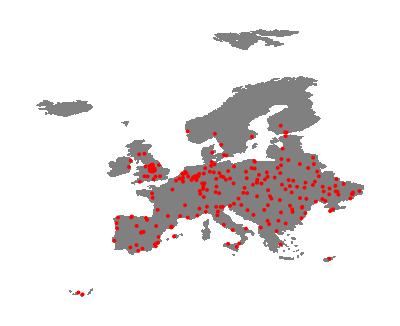

```mathematica
map1 =Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.007],
Point[Reverse[#[[2]]&/@coords,2]]}}]] (*Übersicht über die in der Simulation beteiligten Städte*)
```

Fortfolgend wird nun eine Liste aus Land- und Luftverbindungen erstellt. Mathematica weist Städten geographische Koordinaten zu, welche die Form {Breitengrad,Längengrad} haben. Mit diesen lässt sich alleridngs normalerweise nicht eine Entfernungsmessung durchführen, da sie Winkeln entsprechen. Um das Problem zu umgehen könnte man eine Kugelkoordinatentransformation machen und mit Hilfe des Erdradius und des von zwei Positionsvektoren eingeschlossenen Winkels θ zweier Ortsvektoren die Länge eines Kreissegments bestimmen, also prinzipiell der Abstand auf einer Karte der Erdkugel. Mathematica liefert diese Operation in Kompkatform mit dem "GeoDistance"- Befehl. Folgend wird also eine Liste der Nachbarstädte erstellt mit Abstand < 500 km.

```mathematica
land0 := Table[{cities[[i]],Select[Table[{Delete[coords,i][[j]][[1]],GeoDistance[coords[[i]][[2]],Delete[coords,i][[j]][[2]]]},{j,Length[coords]-1}],#[[2]] <= 500*10^3&]},{i,Length[coords]}];(*Liste aller Landverbindung in der Form {Stadt,{{Nachbarstadt1,Distanz1},...,}}*)
```

Die verzögerte Zuweisung hat den Sinn, dass Mathematica nicht zwangsweise bei jedem neuen Evaluieren des Notebooks die Liste neuberechnen muss. Die "land0"-Liste wird nun dem Export-Befehl überwiesen und somit auch für das Exportieren der Liste erstellt.

```mathematica
Export["land.txt",land0]
land = ReadList["land.txt"];
```

land.txt

Der Export-Befehl ist auskommentiert worden, da die Liste schon in vorherigen Evaluationen des Notebooks erstellt wurde. Sollte dieses Notebook das erste mal evaluiert werden, so muss der Kommentar wieder der Programmzeile zugewiesen werden und die Zelle einmalig ausgewertet wurden. Für jegliche weitere Evaluationen muss nun lediglich der "ReadList"-Befehl einmalig ausgewertet werden, dies spart Rechenzeit im hohen Maß.

```mathematica
lcon = Flatten[Table[Table[{Reverse[CityData[land[[i]][[1]],"Coordinates"]],Reverse[CityData[land[[i]][[2]][[j]][[1]],"Coordinates"]]},{j,Length[land[[i]][[2]]]}],{i,Length[land]}],1]; (*Liste aller Landverbindungen in Form von {Ausgangsstadt-Koordinate,Nachbarstadt-Koordinate}; nur relevant für die Übersichtskarte*)
```

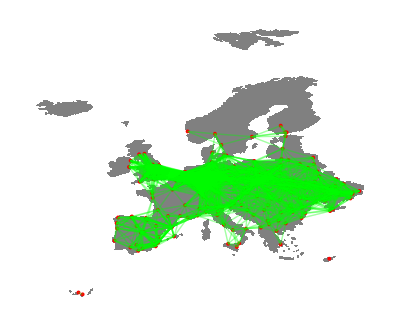

```mathematica
map2 = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.007],
Point[Reverse[#[[2]]&/@coords,2]]},{Green,Opacity[0.2],Line[lcon]}}]] (*Darstellung aller Landverbindungen*)
```

Der nächste Schritt wäre nun die Luftverbindungen zu erschaffen. Diese werden nach der Idee modelliert, dass alle Städte mit EWZ ≥10^6 über Flughäfen verfügen, die sie mit anderen Städten mit 10^6 Einwohnern verbinden. Bei der Erstellung der "cities"-Liste wurde auf eine "clist5" zurückgegriffen, welche lediglich alle Städte mit 2x10^5 Einwohnern aussortiert. Nimmt man selbige "clist5" und stellt das Auswahlkriterium nun auf ≥10^6 Einwohner,
so hat man prinzipiell schon alle an den Luftverbindungen beteiligten Städte.

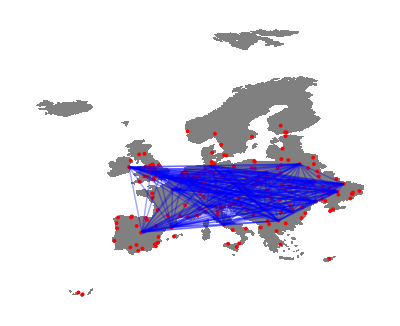

```mathematica
clist6 = Sort[Select[clist4,#[[4]] >= 1*10^6&]](*Städte mit mehr als 1x10^6 EW*);
clist7 = Sort[Select[clist4,#[[4]] >= 2*10^6&]](*Städte mit mehr als 2x10^6 EW*);
air = Permutations[clist6,{2}]; (*Liste aller Städte mit Flugverbindungen*)
aircitycoords =Table[{Reverse[CityData[{air[[i]][[1]][[1]],air[[i]][[1]][[2]],air[[i]][[1]][[3]]},"Coordinates"]],Reverse[CityData[{air[[i]][[2]][[1]],air[[i]][[2]][[2]],air[[i]][[2]][[3]]},"Coordinates"]]},{i,Length[air]}]; (*Koordinaten der Städte mit Flugverbindungen; nur relevant für Übersichtskarte*)
map3 = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.007],
Point[Reverse[#[[2]]&/@coords,2]]},{Blue,Opacity[0.2],Line[aircitycoords]}}]] (*Darstellung aller Luftverbindungen*)
map4 = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.007],
Point[Reverse[#[[2]]&/@coords,2]]},{Green,Opacity[0.2],Line[lcon]},{Blue,Opacity[0.2],Line[aircitycoords]}}]];(*Darstellung aller Verbindungen. Nur relevant für Übersicht im nächsten Teil*)
```

Prinzipiell sind wir also nun fertig mit Teil 1 der Simulation. Wir haben Listen erstellt in welche Städte, Populationen, Land- und Luftverbindungen indiziert sind. Eine kurze Zusammenfassung über das zur Verfügung stehende Werkzeug soll nun folgende Inputzeile liefern:

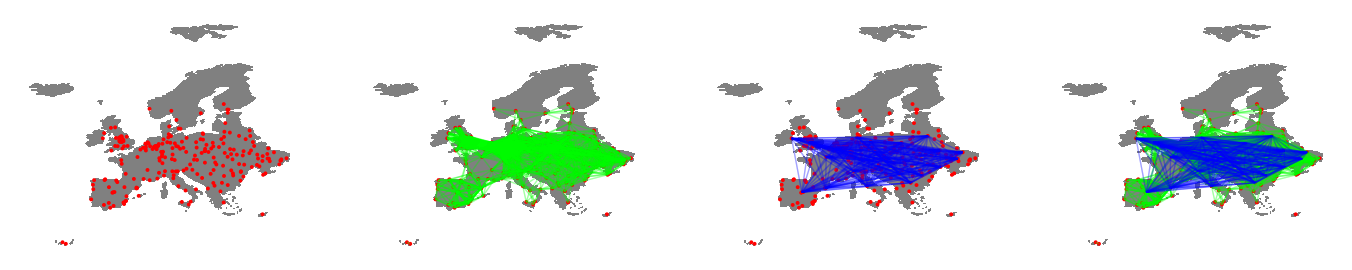

```mathematica
countries; (*Liste aller an der Simulation beteiligten Länder*)
cities; (*Liste aller an der Simulation beteiligten Städte*)
pop; (*Liste der zu den Städten zugehörigen Populationszahlen*)
land; (*Liste der zu den Städten zugehörigen Landverbindungen*)
air; (*Liste der zu den Städten zugehörigen Luftverbindungen*)
GraphicsGrid[{{map1,map2,map3,map4}}] (*Übersicht über die Europa und seine Verkehrsbindungen*)
```

Erste Probleme des verwendeten Modells zeigen sich hierbei schon auf. So unterscheidet das Modell nicht zwischen durch Tourismus und Wirtschaft erzeugtem Vekehrsaufkommen. Die Folge davon ist, dass beliebte Urlaubsgebiete, insbesondere in dieser Simulation die Kanaren, nicht über Flughäfen verfügen, obwohl dies in der Realität der Fall ist. Da zudem Touristen auch nicht als Einwohner gezählt werden hat dies in der Simulation zur Folge, dass die Tourismuszentren schlicht an Bedeutung verlieren. Ein zusätzlicher verfälschender Faktor in der Simulation ist, dass geografische Besonderheiten nicht berücksichtigt werden. Sehr anschaulich zeigt sich dies bei folgender Betrachtung: Sieht man von Fährverkehr und real-existierenden Landverbindungen über Brücken ab, so sollte sich Europa bzgl. seiner Städte annähernd wie eine konvexe Menge verhalten. Alle Landverbindungen sollten daher nur durch Festland führen und nicht durch Gewässer gehen. Dies ist jedoch im bisherigen Modell nicht der Fall. Um zwei Städte zu verbinden wird stets der kürzeste Abstand gewählt, auch wenn dieser nicht realistisch ist. Die Konsequenz dieses Modellfehlers ist, dass bestimmte Städte an Bedeutung als Knotenpunkte innerhalb einer Region verlieren. So ist dies vor allem bei Städten in Großbritannien der Fall, welche aufgrund ihrer direkten Nähe zu Städten in den Niederländen eine hohe Konnektivität zum Festland aufweisen. Das führt dazu, dass sowohl in Großbritanien als auch Niederlanden und Frankreich Hafenstädte an Bedeutung verlieren. Ähnlich verhält sich dies auch bei der Apennin-Halbinsel, welche so z.B. über zahlreiche Direktverbindungen zur Balkan-Halbinsel verfügt. Innerkontinental existiert das Problem auch vor allem in Bezug auf Gebirgsketten, welche in unserem Modell schlicht als nicht existent angenommen werden. Das Problem macht sich vor allem bei den Alpen bemerkbar. So weisen Städte dort barrierefreie Nord-Süd-Verbindungen auf, obwohl man eigentlich eher erwarten würde, obwohl in der Realität eigentlich eher bestimmte Städte Verkehrsknotenpunkte darstellen sollte.

### Teil 2: Grundlegende Populationsdynamik einer Stadt

Mit dem nun zur Verfügung stehenden Werkzeug wollen wir nun einen Schritt weiter gehen und das Reiseverhalten einer Stadt simulieren. Dazu werden wir im folgenden drei verschiedene Module entwickeln welche dieses beschreiben werden. Zunächst legen jedoch erstmal die wesentlichen Parameter des SIR-Modells fest.

```mathematica
pt = 0.1;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate derKrankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
```

Nun geht es daran da Reiseverhalten zu simulieren. Das Reiseverhalten setzt sich in unserem Netzwerk aus Land - und Luftverkehr zusammen. Dementsprechend werden wir nun folgend zwei Module travelAir[ ] und travelLand[ ] erstellen welche diesen Prozess für eine Stadt berechnen. Diese Module werden dann später auf alle im Netzwerk vorhandenen Städte verallgemeinert.

Die Startparameter für die Module werden in in den sus0-, inf0- und rec0-Listen abgelegt. Wobei wir für Testzwecke die Zahl der Infizierten in London auf 1000 setzen wollen. Dafür brauchen wir erst die Listen-Position von London. Durch Anwendung des CityData-Befehl auf den Namen "London" erhalten wir eine Liste aller Städte mit selbigen Namen. Für London stellt in diesem Falle direkt das erste Element der Liste, das London in Europa dar. Durch Anwedung des Position-Befehls auf die cities-Liste erhalten wir nun die Listenposition von London.

```mathematica
Position[cities,CityData["London"][[1]]]
```

{{123}}

Nun können wir die Startparameter festlegen. Für die Susceptibles werden direkt die Populationszahlen der Städte übernommne, bei den Infectives soll lediglich London (Listenposition 123)  1000 Infizierte kriegen. Die Zahlen der Recovered bleiben für jede Stadt auf 0 gestellt. Die einzelnen Gruppen-Listen haben die Form Gruppe1 = {0, {GruppenpopulationStadt1,...,GruppepopulationStadt230}}. Das erste Element einer solchen Gruppe ist die 0. Die 0 sagt lediglich aus, dass dies der Zustand dieser Bevölkerungsgruppe im Netzwerk für den 0ten Tag ist. Die einzelnen Gruppen-Listen werden dann in eine Gesamtliste namens sir0 überführt, welche alle Anfangsbedingungen für den Start einer Simulation enthält.

```mathematica
sus1 = {0,pop}; (*Anfangswerte für Susceptibles *)
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]}; (*Anfangswerte für Infectives*)
rec1 = {0,Table[0,{i,Length[pop]}]}; (*Anfangswerte für Recovered*)
sir0 = {sus1,inf1,rec1};
```

Nun soll der Bevölkerungaustausch durch Landreisevekehr für eine Stadt berechnet werden. Das Modul soll also variabel in den Anfangsbedingungen sowie der Stadt sein, für welche der Reisestrom berechnet wird.

```mathematica
travelLand[{sus0_,inf0_,rec0_},i_]:=Module[{ω,trsus,trinf,trrec,land2,listpos,change0,change1,change2,change3,change4,popnow,omegas},
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
ω[z_] := (2*pt)/(Length[land[[i]][[2]]]+Length[land[[z]][[2]]]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus= sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)
land2 =Table[land[[i]][[2]][[j]][[1]],{j,Length[land[[i]][[2]]]}]; (*Liste aller Nachbarstädte, ohne Entfernung zur Ausgangsstadt*)
listpos = Table[Position[cities,land2[[j]]][[1]],{j,Length[land2]}];
change0 =Table[{0,0,0},{j,Length[cities]}];  (*Erstellt eine leere Liste welche als Speicher für die berechnete Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{1,1,1}ω[j]],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{trsus,trinf,trrec}];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = Table[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]}*omegas[[j]][[1]],{j,1,Length[change2]}];
change4 = ReplacePart[change3, {i} -> -Sum[{change3[[j]][[1]],change3[[j]][[2]],change3[[j]][[3]]},{j,Length[change2]}]];
If[Length[change4]==0,Return[0],Return[change4]
];
];
```

```mathematica
travelLand[sir0,223]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{647.457,0.,0.},{1305.08,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{830.28,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1180.81,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{886.426,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{796.766,0.,0.},{0,0,0},{0,0,0},{1044.04,0.,0.},{0,0,0},{0,0,0},{0,0,0},{2208.37,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{643.9,0.,0.},{0,0,0},{0,0,0},{0,0,0},{902.636,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{983.853,0.,0.},{0,0,0},{0,0,0},{857.779,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1822.14,0.,0.},{0,0,0},{1365.74,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1032.64,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1657.03,0.,0.},{1427.26,0.,0.},{0,0,0},{0,0,0},{1207.69,0.,0.},{0,0,0},{892.431,0.,0.},{0,0,0},{0,0,0},{686.04,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{741.886,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1204.1,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1288.41,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{761.992,0.,0.},{1183.84,0.,0.},{0,0,0},{0,0,0},{0,0,0},{700.523,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1023.76,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{929.121,0.,0.},{0,0,0},{885.05,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{952.959,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1006.81,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{-33056.8,0.,0.},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

Das trLand[]-Modul berechnet also nun die reinen Änderungen der Populationen aufgrund des Landverkehrs. Die Quintessenz des Moduls liegt im Wichtungsfaktor w. Mit diesem berechnet sich zusammen mit der Populationszahl einer SIR-Population und der Reisewahrscheinlichkeit pt, wie viele Menschen pro Population in eine einzige Nachbarstadt ausrücken. Hat eine Stadt n>0 Nachbarstädte, so kann man schlicht das Reziproke der Nachbarstadt-Anzahl zur Gewichtung nehmen, also w(n)≡1/n. Hat eine Stadt keine Nachbarstädte, so findet logischerweise auch kein Reiseverkehr statt. Der einzigst logische Schluß ist daher, den Wichtungsfaktor w(0)≡0 zu setzen. Es ist anzumerken, dass der Bevölkerungsaustausch in diesem Modul nach der Idee modelliert wurde, dass im Mittel jede Ausgangsstadt in ihre Nachbarstädte eine gleiche Anzahl an Menschen sendet. Dies ist in der Realität natürlich nicht so und es ist durchaus diskutabel ob die Verwendung von Zufallszahlen, oder zusätzlichen Faktoren zur Steuerung der Reiseströme sinnvoller wäre. Nun wird das "travelAir"-Modul erstellt:

```mathematica
travelAir[{sus0_,inf0_,rec0_},i_]:=Module[{ω,air2,air3,listpos,change0,change1,change2,change3,change4,trsus,trinf,trrec,popnow,omegas},
air2=Table[{{air[[j]][[1]][[1]],air[[j]][[1]][[2]],air[[j]][[1]][[3]]},{air[[j]][[2]][[1]],air[[j]][[2]][[2]],air[[j]][[2]][[3]]}},{j,Length[air]}] ;(*Erzeugt Liste der Luftverbindungen ohne Bevölkerungszahlen*)
air3 = Select[air2,(#[[1]]==cities[[i]])&] ;(*Liste aller Nachbarstädte*)
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
ω[z_] := (2*pt)/(Length[air3]+Length[air3]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus =sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)
listpos = Table[Position[cities,air3[[j]][[2]]][[1]],{j,Length[air3]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[cities]}]; (*Erstellt eine leere Liste welche als Speicher für die berechnete Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{1,1,1}ω[j]],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{trsus,trinf,trrec}];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = Table[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]}*omegas[[j]][[1]],{j,1,Length[change2]}];
change4 = ReplacePart[change3, {i} -> -Sum[{change3[[j]][[1]],change3[[j]][[2]],change3[[j]][[3]]},{j,Length[change2]}]];
If[Length[change4]==0,Return[0],Return[change4]
];
];
```

Nun können wir also die gesamte Land- und Luftreisevekehrsbewegung berechnen. Der verwendete Listen-Formalismus macht die Berechnung der gesamten Reisebewegung zusätzlich sehr einfach, da man schlicht das jeweilige Modul über einem Iterator aufsummieren muss.

```mathematica
travelLandAll[{sus0_,inf0_,rec0_}] := Module[{a,sus,inf,rec},
Clear[sus,inf,rec];
a= Sum[travelLand[{sus0,inf0,rec0},j],{j,1,Length[sus0[[2]]]}];(*Summiert alle Bevölkerungs-Änderungen über alle Städte auf*)
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};(*Erzeugt sus-Liste aus obiger Summe*)
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};(*Erzeugt inf-Liste aus obiger Summe*)
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};(*Erzeugt rec-Liste aus obiger Summe*)
Return[{sus,inf,rec}] 
];

travelAirAll[{sus0_,rec0_,inf0_}] := Module[{a,sus,inf,rec},
Clear[sus,inf,rec];
a= Sum[travelAir[{sus0,rec0,inf0},j],{j,1,Length[sus0[[2]]]}]; (*Summiert alle Bevölkerungs-Änderungen über alle Städte auf*)
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};(*Erzeugt sus-Liste aus obiger Summe*)
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};(*Erzeugt inf-Liste aus obiger Summe*)
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};(*Erzeugt rec-Liste aus obiger Summe*)
Return[{sus,inf,rec}]
];
```

Wir können jetzt also mit Hilfe obiger Module die gesamte Reisebewegung berechnen. Allerdings ignorieren bisweilen den Charakter der Krankheitsausbreitung selbst. Daher wäre nun der nächste Schritt die Evolution der SIR-Populationen für die einzelnen Städte durchzurechnen. Zur Berechnungen der Evolution nach dem SIR-Modell müssen Differentialgleichungen gelöst. Für die Lösung der Differentialgleichungen kommen unterschiedliche Methoden in Frage. Die folgenden Module werden die Variablen {sus0,inf0,rec0} und j besitzen. Die erste Variable weist dem Modul eine Liste aus Anfangswerten für die SIR-Populationen aus welcher dann mit der zweiten Variable eine j-te Stadt rausgegriffen werden kann. Empfehlenswert für Tests der Module sind Städte mit großen Einwohnerzahlen hoher Konnektivität. Bei diesen machen sich wesentliche Eigenschaften der Simulation am stärksten bemerkbar. Eine solche Stadt wäre z.B. für j≡123, London in Großbritannien. Als erstes probieren wir den Mathematica-internen NDSolve-Befehl aus, welcher auf Basis von Mathematica-internen Algorithmen die "beste" Lösungsmethode raussucht.

```mathematica
InfectNDS[{sus0_,inf0_,rec0_},j_] := Module[{susct,infct,recct,eq1,eq2,eq3,eq4,eq5,eq6,sol,s,i,r},
eq1 = (s'[t]==-beta*s[t]*i[t]/(s[t]+i[t]+r[t])-mu*s[t]+mu*(s[t]+i[t]+r[t]));
eq2 = (i'[t]==beta*i[t]*s[t]/(s[t]+i[t]+r[t])-nu*i[t]-mu*i[t]);
eq3=(r'[t]==nu*i[t]-mu*r[t]);
eq4 = (s[0]==sus0[[2]][[j]]);
eq5=(i[0]==inf0[[2]][[j]]);
eq6 =(r[0]==rec0[[2]][[j]]);
sol :=NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6},{s[t],i[t],r[t]},{t,0,1}];
Return[Round[({s[t],i[t],r[t]}/.sol)/.{t->1}][[1]]]
]
```

Der nächste Schritt wäre explizit die Euler-Methode zu verwenden:

```mathematica
InfectEuler[{sus0_,inf0_,rec0_},j_] := Module[{fs,fi,fr,Δ,t},
Clear[i];
s[0]=sus0[[2]][[j]];
i[0]=inf0[[2]][[j]];
r[0]=rec0[[2]][[j]];
fs[t_,Δ_]=s[t]+Δ*(-beta*s[t]*i[t]/(s[t]+i[t]+r[t])-mu*s[t]+mu*(s[t]+i[t]+r[t]));
fi[t_,Δ_]=i[t]+Δ*(beta*i[t]*s[t]/(s[t]+i[t]+r[t])-nu*i[t]-mu*i[t]);
fr[t_,Δ_]=r[t]+Δ*(nu*i[t]-mu*r[t]);
Return[Round[{fs[t,Δ],fi[t,Δ],fr[t,Δ]}/.{t->0,Δ->1}]]
];
```

Machen wir es einen Schritt genauer mit der Runge-Kutta-Methode:

```mathematica
InfectRK4[{sus0_,inf0_,rec0_},j_] :=Module[{Δ,a,b,c,F,k1,k2,k3,k4,sus1,inf1,rec1,sus2,inf2,rec2},
Δ=1;
a=-beta*s[t]*i[t]/(s[t]+i[t]+r[t])-mu*s[t]+mu*(s[t]+i[t]+r[t]);
b=beta*i[t]*s[t]/(s[t]+i[t]+r[t])-nu*i[t]-mu*i[t];
c =nu*i[t]-mu*r[t];
F = {a,b,c};
k1 = F /. {s[t] -> sus0[[2]][[j]],i[t] -> inf0[[2]][[j]],r[t] -> rec0[[2]][[j]]};
k2  = F /. {s[t] -> sus0[[2]][[j]]+k1[[1]]/2,i[t] -> inf0[[2]][[j]]+k1[[2]]/2,r[t] -> rec0[[2]][[j]]+k1[[3]]/2};
k3 = F /. {s[t] -> sus0[[2]][[j]]+k2[[1]]/2,i[t] -> inf0[[2]][[j]]+k2[[2]]/2,r[t] -> rec0[[2]][[j]]+k2[[3]]/2};
k4 = F /. {s[t] -> sus0[[2]][[j]]+k3[[1]],i[t] -> inf0[[2]][[j]]+k3[[2]],r[t] ->rec0[[2]][[j]]+k3[[3]]/2};
sus2 = 1/6*(k1[[1]]+2*k2[[1]]+2*k3[[1]]+k4[[1]]);
inf2 = 1/6*(k1[[2]]+2*k2[[2]]+2*k3[[2]]+k4[[2]]);
rec2 = 1/6*(k1[[3]]+2*k2[[3]]+2*k3[[3]] +k4[[3]]);
Return[{sus0[[2]][[j]]+Round[sus2],inf0[[2]][[j]]+Round[inf2],rec0[[2]][[j]]+Round[rec2]}]
];
```

Welche Methode ist nun die für die Simulation am besten geeignete? Hinsichtlich der Genaugikeit wäre die Runge-Kutta-Methode empfehlenswert, während Erwartungsgemäß die Euler-Methode schneller aber ungenauer wäre. Offen bleibt jedoch die Frage nach der Effizienz des Mathematica-internen NDSolve-Befehls. Dieser basiert auf Algorithmen welche automatisch die "geeigneteste" Lösungsmethode raussuchen. Natürlich gehört zu den geeignete Lösungsmethoden auch RK4 und Euler. Die Antwort auf unsere Fragen sollte der direkte Vergleich liefern. Führen wir also die Module für London (j≡123) aus und Vergleichen Geschwindigkeit und Zahlenwerte der einzelnen Methoden:

```mathematica
InfectNDS[sir0,123]
InfectEuler[sir0,123] 
InfectRK4[sir0,123]
```

{7753499,1030,71}

{7753500,1030,70}

{7753499,1030,71}

Die rein numerischen Unterschiede zwischen den Methoden sind ersichtlich gering. Der NDSolve-Befehl scheint eine Methode gewählt zu haben die nahezu exakt gleiche Werte wie die RK4-Methode liefert. Die Euler-Methode zeigt als einzigste Methode eine Abweichung, diese betrifft aber nur eine einzigste Person innerhalb einer Stadt ~ 8 Millionen. Es sollte daher wohl nur einen geringen Unterschied machen welche Methode man verwendet. Welches Modul ist aber nun das schnellste?

```mathematica
Timing[InfectNDS[sir0,123]][[1]]
Timing[InfectEuler[sir0,123]][[1]]
Timing[InfectRK4[sir0,123] ][[1]]
```

0.

0.

0.

Offensichtlich sind die Geschwindigkeiten aller Module recht hoch. Es ist daher durchaus vertretbar die geringfügig präzisere RK4-Methode zu verwenden. 
Der nächste Schritt besteht nun darin unsere Module welche die SIR-Populationen berechnen auf alle Städte verallgemeinern. In den folgenden Modulen wird schlicht die einzelne Lösungsmethode für 
alle an der Simulation beteiligten Städte durchlaufen gelassen.

```mathematica
InfectNDSAll[sir0_]:=Module[{susNDS,infNDS,recNDS,a},
a= Table[InfectNDS[sir0,j],{j,1,Length[sir0[[1]][[2]]]}];
susNDS = Table[a[[j]][[1]],{j,1,Length[sir0[[1]][[2]]]}]; 
infNDS = Table[a[[j]][[2]],{j,1,Length[sir0[[1]][[2]]]}]; 
recNDS = Table[a[[j]][[3]],{j,1,Length[sir0[[1]][[2]]]}]; 
Return[{susNDS,infNDS,recNDS}]
];
```

```mathematica
InfectEulAll[sir0_]:=Module[{susEul,infEul,recEul,a},
a= Table[InfectEuler[sir0,j],{j,1,Length[sir0[[1]][[2]]]}];
susEul = Table[a[[j]][[1]],{j,1,Length[sir0[[1]][[2]]]}]; 
infEul = Table[a[[j]][[2]],{j,1,Length[sir0[[1]][[2]]]}]; 
recEul = Table[a[[j]][[3]],{j,1,Length[sir0[[1]][[2]]]}]; 
Return[{susEul,infEul,recEul}]
];
```

```mathematica
InfectRK4All[sir0_]:=Module[{susRK4,infRK4,recRK4,a},
a= Table[InfectRK4[sir0,j],{j,1,Length[sir0[[1]][[2]]]}];
susRK4 = Table[a[[j]][[1]],{j,1,Length[sir0[[1]][[2]]]}]; 
infRK4 = Table[a[[j]][[2]],{j,1,Length[sir0[[1]][[2]]]}]; 
recRK4 = Table[a[[j]][[3]],{j,1,Length[sir0[[1]][[2]]]}]; 
Return[{susRK4,infRK4,recRK4}]
];
```

### Teil 3: Erstellung der simulations-kritischen Module

Fassen wir nun die Ergebnisse aus Teil 1 und Teil 2 kurz zusammen. Wir haben nun prinzipiell die wesentlichen Bestandteile der Simulation fertig und können diese sprichwörtlich zusammenstecken. Es fehlt lediglich eines entsprechenden Simulations-Befehl welcher für eine angegebene Spanne an Tagen die Populationsentwicklung berechnet. Haben wir diese berechnet, so wäre es auch gut über geeignete Mittel zur Visualisierung zur verfügen. Dafür würde sich direkt unsere Europa-Karte aus Teil 1 empfehlen. 
Zunächst erstmals zu den Simulationsmodulen selber. Diese haben die Variablen {sus0,inf0,rec0} und days. Wie zuvor schon erwähnt gibt die erste Liste die Anfangswerte an die Simulation über, während die zweite Variable bestimmt für wie viele Tage die Simulation durchgerechnet werden soll. Sollten 0 Tage eingeben werden, so werden die Anfangswerte des Moduls direkt wiedergegeben. Für alle weiteren Werte errechnet das Simulationsmodul eine Liste der Populationen für die jeweiligen Tage.

```mathematica
SimulateNDS[{sus0_,inf0_,rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,cont,i},
i=1;
cont ={};
cont =Append[cont,{sus0,inf0,rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelLandAll[{susS1,infS1,recS1}];
{susS3,infS3,recS3} = {susS2,infS2,recS2}+travelAirAll[{susS2,infS2,recS2}];
{susS4,infS4,recS4}=InfectNDSAll[{susS3,infS3,recS3}];
{sus,inf,rec}={{i,susS4},{i,infS4},{i,recS4}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

```mathematica
SimulateEuler[{sus0_,inf0_,rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,cont,i},
i=1;
cont ={};
cont =Append[cont,{sus0,inf0,rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelLandAll[{susS1,infS1,recS1}];
{susS3,infS3,recS3} = {susS2,infS2,recS2}+travelAirAll[{susS2,infS2,recS2}];
{susS4,infS4,recS4}=InfectEulAll[{susS3,infS3,recS3}];
{sus,inf,rec}={{i,susS4},{i,infS4},{i,recS4}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

```mathematica
SimulateRK4[{sus0_,inf0_,rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,cont,i},
i=1;
cont ={};
cont =Append[cont,{sus0,inf0,rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelLandAll[{susS1,infS1,recS1}];
{susS3,infS3,recS3} = {susS2,infS2,recS2}+travelAirAll[{susS2,infS2,recS2}];
{susS4,infS4,recS4}=InfectNDSAll[{susS3,infS3,recS3}];
{sus,inf,rec}={{i,susS4},{i,infS4},{i,recS4}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

Zur Visualisierung der Europa-Karte benötigen wir eine Funktion welche die Punkte mit denen die Städte dargestellt werden entsprechend einfärbt. Dafür wird nun folgend das tmc-Modul erstellt welches die Grafikausgabe für eine Stadt liefert mit RGB-Wert und Position. Der RGB-Wert ist eine Funktion in Abhängigkeit der Nicht-Infizierten und Infizierten. Kommt ein Infizierter in einer Stadt an, so wird diese automatisch grün eingefärbt. Städte ohne Infizierte bleiben dagegen rot gefärbt.

```mathematica
tmc[SimInput_,i_,j_] := Module[{Sim,SumPop,SusPop,InfPop,RecPop},
Clear[Sim];
Sim = SimInput;
SumPop:=Sim[[j]][[1]][[2]][[i]]+Sim[[1]][[2]][[2]][[i]]+Sim[[1]][[3]][[2]][[i]];
SusPop :=Sim[[j]][[1]][[2]][[i]];
InfPop :=Sim[[j]][[2]][[2]][[i]];
RecPop := Sim[[j]][[3]][[2]][[i]];
Return[{RGBColor[HeavisideTheta[SusPop-0.01]-HeavisideTheta[InfPop-0.01],HeavisideTheta[InfPop-0.01]*Log[E+InfPop]/Log[E+InfPop+RecPop],Log[E+RecPop]/Log[E+InfPop+RecPop]*HeavisideTheta[InfPop-0.01]],PointSize[0.005+0.005*HeavisideTheta[InfPop-0.01]],Point[Reverse[coords[[i]][[2]]]]}]
];
```

Wie ersichtlich wurde im tmc-Modul die Heaviside-Theta-Funktion benutzt. Da diese an der Stelle 0 nicht definiert ist und für x > 0 gleich 1 ist wurde ein Korrekturfaktor von 0.01 eingefügt, der verhindert dass die Theta-Funktion nicht ausgewertet wird. Das tmc-Modul liefert nun das nötige Werkzeug um eine Darstellung der Simulationsdaten zu erzeugen. Im folgenden wird noch ein Visualize-Modul erstell welches durch schlichte Eingabe von Simulationsdaten eine Visualisierung erzeugt.

```mathematica
Visualize[SimInput_]:=Module[{colorlist,colorlist2},
Clear[colorlist,colorlist2];
colorlist = Table[Table[tmc[SimInput,i,j],{j,1,Length[SimInput]}] ,{i,Length[SimInput[[1]][[1]][[2]]]}];
colorlist2 =Transpose[colorlist];
Manipulate[Graphics[{Background->LightGray,{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]}]},colorlist2[[k]]}],{k,1,Length[SimInput],1}]
];
```

### Teil 4: Start der Simulation

#### Vergleich der einzelnen Lösungsmethoden

Folgend möchten wir die einzelnen Lösungsmethoden vergleichen. Um brauchbare Daten zu erhalten müssen die Parameter der Simulation dementsprechend gewählt werden. Momentan sind im Kernel noch die alten Parameter aus Teil 2 abgespeichert mit einer Reisewahrscheinlichkeit p_t=0.01. Rechnen wir nun mit dieser das Reiseverhalten der Londoner durch:

```mathematica
travelLand[sir0,123][[123]]
```

{-119457.,-15.4066,0.}

Es reisen offensichtlich aus 1000 Infizierten Londonern 0 ab. Daher modifizieren wir die Reisewahrscheinlichkeit.

```mathematica
pt = 0.25;
travelLand[sir0,123][[123]]
```

{-298642.,-38.5166,0.}

Jetzt reisen 42 Infizierte ab. Diese Zahl sollte nach der Zeit bemerkbare Veränderungen in der Simulation bewirken. Definieren wir also unsere Parameter nochmals alle neu:

```mathematica
pt = 0.25;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate derKrankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
sus1 = {0,pop};
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]};
rec1 = {0,Table[0,{i,Length[pop]}]};
sir0 = {sus1,inf1,rec1};
```

Starten wir nun die Simulationen mit den verschiedenen Lösungsmethoden und lassen uns gleichzeitig die einzelnen Rechenzeiten berechnen:

```mathematica
sim01= Timing[SimulateNDS[sir0,30]];
sim02= Timing[SimulateEuler[sir0,30]];
sim03= Timing[SimulateRK4[sir0,30]];
```

Wir speichern die Simulationsdaten unter den Namen SimNDS, SimEul und SimRK4 ab.

```mathematica
SimNDS= sim01[[2]];
SimEul= sim02[[2]];
SimRK4= sim03[[2]];
```

Nun vergleichen wir die einzlenen Lösungsmethoden miteinander:

```mathematica
sim01[[1]]
sim02[[1]]
sim03[[1]]
```

98.655

95.176

99.763

In dieser Ausführung des Notebooks zeigt sich, dass die Euler-Methode am schnellsten mit 120.62 Sekunden arbeitet. Am zweit schnellsten ist der Mathematica-interne NDS-Befehl mit 126.72 Sekunden und am längsten dauert die RK4-Methode mit 136.30 Sekunden. Vergleichen wir die Zeitentwicklung der Simulationen mit Hilfe des Visualize-Moduls nun:

```mathematica
GraphicsGrid[{{Visualize[SimNDS],Visualize[SimEul],Visualize[SimRK4]}}]
```

-Graphics-

Augenscheinlich scheint der Ausgang der Simulation nur geringfügig durch die numerische Methode beeinflusst zu werden. Einen genauen Überblick können wir allerdings erst erhalten, indem wir die Listen der Infizierten am 30sten Tag vergleichen:

```mathematica
SimNDS[[31]][[2]]
SimEul[[31]][[2]]
SimRK4[[31]][[2]]
```

{30,{1,0,0,0,2,5,0,0,1,0,0,0,2,0,3,1,0,2,0,2,0,0,14,2,0,6,0,9,0,0,0,4,0,8,0,1,6,10,2,0,41,0,0,6,1,0,0,0,0,0,4,0,0,0,8,0,0,0,8,0,19,0,3,0,29,8,6,16,9,0,2,0,7,0,4,4,0,0,0,6,0,13,0,7,0,0,0,4,5,7,0,0,0,0,0,0,7,0,0,2,0,0,2,0,5,14,0,0,0,9,0,0,0,11,26,4,0,22,0,12,0,0,504,3,0,0,0,0,0,24,4,0,0,0,0,23,8,0,0,0,7,5,10,0,0,13,10,0,0,18,0,0,0,25,5,15,17,0,0,0,0,0,0,0,71,0,0,25,0,0,0,7,0,0,30,18,0,0,30,28,0,0,0,0,0,24,0,0,3,0,21,0,20,16,7,0,0,0,0,0,36,0,0,0,0,0,0,0,22,0,0,0,0,0,8,0,0,0,0,0,42,12,33,0,13,0,0,0,0,7}}

{30,{1,0,0,0,2,4,0,0,1,0,0,0,2,0,2,1,0,2,0,2,0,0,13,2,0,5,0,9,0,0,0,4,0,8,0,1,6,9,2,0,39,0,0,6,1,0,0,0,0,0,4,0,0,0,8,0,0,0,8,0,19,0,3,0,28,7,6,15,8,0,2,0,6,0,4,4,0,0,0,5,0,13,0,7,0,0,0,4,4,7,0,0,0,0,0,0,7,0,0,2,0,0,2,0,5,14,0,0,0,9,0,0,0,10,25,3,0,21,0,12,0,0,498,3,0,0,0,0,0,23,4,0,0,0,0,22,7,0,0,0,7,5,10,0,0,13,9,0,0,17,0,0,0,24,5,14,16,0,0,0,0,0,0,0,70,0,0,24,0,0,0,7,0,0,30,17,0,0,30,28,0,0,0,0,0,24,0,0,3,0,20,0,19,15,6,0,0,0,0,0,35,0,0,0,0,0,0,0,22,0,0,0,0,0,7,0,0,0,0,0,41,11,31,0,12,0,0,0,0,7}}

{30,{1,0,0,0,2,5,0,0,1,0,0,0,2,0,3,1,0,2,0,2,0,0,14,2,0,6,0,9,0,0,0,4,0,8,0,1,6,10,2,0,41,0,0,6,1,0,0,0,0,0,4,0,0,0,8,0,0,0,8,0,19,0,3,0,29,8,6,16,9,0,2,0,7,0,4,4,0,0,0,6,0,13,0,7,0,0,0,4,5,7,0,0,0,0,0,0,7,0,0,2,0,0,2,0,5,14,0,0,0,9,0,0,0,11,26,4,0,22,0,12,0,0,504,3,0,0,0,0,0,24,4,0,0,0,0,23,8,0,0,0,7,5,10,0,0,13,10,0,0,18,0,0,0,25,5,15,17,0,0,0,0,0,0,0,71,0,0,25,0,0,0,7,0,0,30,18,0,0,30,28,0,0,0,0,0,24,0,0,3,0,21,0,20,16,7,0,0,0,0,0,36,0,0,0,0,0,0,0,22,0,0,0,0,0,8,0,0,0,0,0,42,12,33,0,13,0,0,0,0,7}}

Tatsächlich sind die Unterschiede der Populationen nach 30 Schritten signifikant gering. Eine Betrachtung der Entwicklung der Infiziertenpopulation von London für NDS (Rot), Euler (Grün) und RK4 (Blau) zeigt selbiges auf.

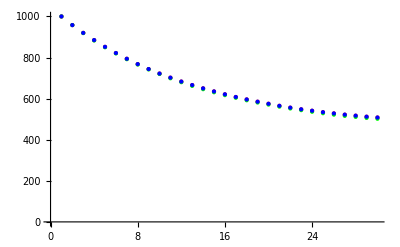

```mathematica
ListPlot[{Table[SimNDS[[i]][[2]][[2]][[123]],{i,1,30}],Table[SimEul[[i]][[2]][[2]][[123]],{i,1,30}],Table[SimRK4[[i]][[2]][[2]][[123]],{i,1,30}]},PlotStyle->{Red,Green,Blue}]
```

Auch der zeitliche Verlauf der von der Krankheit Erholten zeigt keine merkliche Abweichung auf.

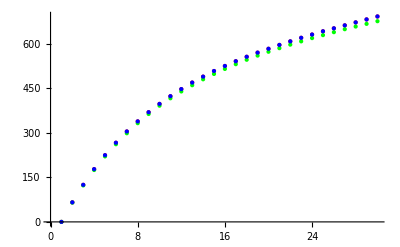

```mathematica
ListPlot[{Table[SimNDS[[i]][[3]][[2]][[123]],{i,1,30}],Table[SimEul[[i]][[3]][[2]][[123]],{i,1,30}],Table[SimRK4[[i]][[3]][[2]][[123]],{i,1,30}]},PlotStyle->{Red,Green,Blue}]
```

Es ist daher durchaus gerechtfertigt die schnellere Euler-Methode für weitere Betrachtungen zu verwenden.

#### Test der Simulation für die explizit vorgegebenen Anfangsparameter

Im folgenden Teil soll das Verhalten der Simulation für die explizit vorgegebenen Anfangsparameter untersucht werden. Es werden dabei die vorgegebenen Paramater verwendet mit p_t=0.01, β= 0.1, ν=0.07, 
μ = 3x10^-5 mit 1000 Infizierten in London. Da die Erholungsrate gleich dem reziproken der Krankheitsdauer ist handelt es sich um Krankheitsdauer von ~14 Tagen. Dies entspricht einem Grippeinfekt. Setzen wir also die Anfangsparameter fest:

```mathematica
pt = 0.01;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate derKrankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
sus1 = {0,pop};
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]};
rec1 = {0,Table[0,{i,Length[pop]}]};
sir0 = {sus1,inf1,rec1};
```

Und starten die Simulation für 30 Tage:

```mathematica
SimPar =SimulateEuler[sir0,30];
```

Nun visualisieren wir die Ausbreitung der Krankheit:

```mathematica
Visualize[SimPar]
```

Augenscheinlich hat sich nach 30 Tagen die Krankheit in Europa nicht weiter ausgebreitet. Betrachten wir daher nun Infizierten-Zahlen am 30sten Tag:

```mathematica
SimPar[[31]][[2]]
```

{30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2221,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Die Krankheit ist also in London geblieben. Betrachten wir nun eine Plot für Populationszahlen der Infizierten (grün) und Erholten (rot):

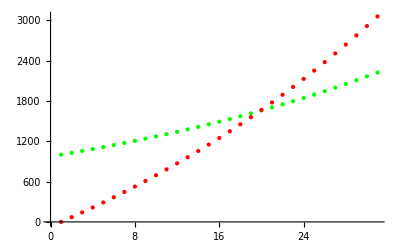

```mathematica
ListPlot[{Table[SimPar[[j]][[2]][[2]][[123]],{j,1,31}],Table[SimPar[[j]][[3]][[2]][[123]],{j,1,31}]},PlotStyle->{Green,Red}]
```

Interessanterweise verhält sich dieser Fall nicht analog wie im Test der Lösungsmethoden. Offensichtlich hat die Wahl der Reisewahrscheinlichkeit einen bedeutenden Einfluß auf die Entwicklung der Infiziertenzahlen innerhalb einer Stadt. Die niedrigere Reisewahrscheinlichkeit scheint in diesem Fall dazu zu führen, dass die Infektionsrate mit positiver Steigung wächst stets wächst. Beim Test der Lösungsmethoden scheint die Reisewahrscheinlichkeit die Infektionszahlen zusammen mit der Erholungsrate zu stark gedrückt zu haben, so dass die Infiziertenzahlen mit negativen Vorzeichen über die Zeit nur abfielen und aufgrund der Kopplung die Zahl der Erholten auch relativ schnell Sättigungsverhalten offenbarte.

#### Weitere Untersuchungen

Setzen wir die Reisewahrscheinlichkeit jetzt auf 0. Zu erwarten wäre ein zu den explizit vorgebenen Parametern ähnliches Verhalten.

```mathematica
pt = 0.00;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate derKrankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
sus1 = {0,pop};
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]};
rec1 = {0,Table[0,{i,Length[pop]}]};
sir0 = {sus1,inf1,rec1};
```

```mathematica
SimNoTravel = SimulateEuler[sir0,30];
```

Offensichtlich sind bis zum 30sten Tag keine Menschen verreist:

```mathematica
SimNoTravel[[31]][[2]]
```

{30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2423,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Das Visualize-Modul bestätigt diese Annahme.

```mathematica
Visualize[SimNoTravel]
```

Wie erwartet verhalten sich die Bevölkerungszahlenanalog wie zum Fall der explizit vorgegebenen Parameter:

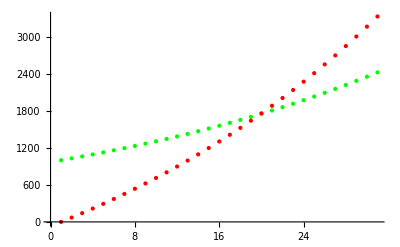

```mathematica
ListPlot[{Table[SimNoTravel[[j]][[2]][[2]][[123]],{j,1,31}],Table[SimNoTravel[[j]][[3]][[2]][[123]],{j,1,31}]},PlotStyle->{Green,Red}]
```

Ein weiterer Fall wäre nun eine Reisewahrscheinlichkeit von 0.5.

```mathematica
pt = 0.5;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate der Krankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
sus1 = {0,pop};
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]};
rec1 = {0,Table[0,{i,Length[pop]}]};
sir0 = {sus1,inf1,rec1};
```

```mathematica
SimAllTravel = SimulateEuler[sir0,30];
```

```mathematica
Visualize[SimAllTravel]
```

Entgegen den Erwartungen führt diese Reisewahrscheinlichkeit lediglich dazu, dass sich die Krankheit in hoher Geschwindigkeit über Europa ausbreitet.

```mathematica
SimAllTravel[[31]][[2]]
```

{30,{0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,2,2,0,10,0,7,0,0,0,6,0,2,1,1,1,3,1,0,62,0,0,2,4,0,0,0,0,0,1,0,0,0,5,0,0,0,6,0,37,0,4,2,31,8,5,21,2,0,1,0,5,0,1,4,0,0,0,4,0,5,0,5,0,0,0,7,7,22,0,0,0,0,0,0,12,0,0,2,0,0,4,0,3,10,0,0,0,10,0,0,0,8,29,7,0,17,0,8,1,0,241,6,0,0,0,0,4,19,7,0,0,0,1,19,9,0,0,0,9,4,11,0,0,17,20,0,0,25,0,0,0,20,9,29,27,0,0,1,0,1,0,0,66,0,0,30,0,0,5,18,0,0,45,25,0,0,23,53,0,0,0,0,0,31,0,0,1,0,28,0,23,39,13,0,6,0,0,0,43,0,0,0,0,0,1,1,32,0,0,0,3,5,8,0,0,0,0,0,47,29,61,2,33,4,0,0,0,27}}

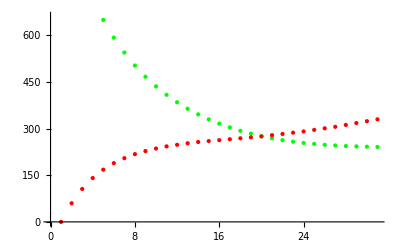

```mathematica
ListPlot[{Table[SimAllTravel[[i]][[2]][[2]][[123]],{i,Length[SimAllTravel]}],Table[SimAllTravel[[i]][[3]][[2]][[123]],{i,Length[SimAllTravel]}]},PlotStyle -> {Green,Red}]
```

Während bei den Test der Lösungsmethoden die Zahl der Erholten für t →∞ sättigte drückt die hohe Reisewahrscheinlichkeit in diesem Falle die Zahl der Erholten so stark, dass das Sättigungsverhalten nicht beobachtet werden kann. Es kommt in der Simulation daher schlicht zu einer starken, europaweiten Umverteilung aller Infizierten und Erholten was sich dementsprechend auf die Entwicklungszahlen beider Populationen auswirkt.

Ein interessanter Fall ergibt sich nun für die Simulation wenn Geburts- und Sterberate abgeschaltet werden sowie die Erholungsrate ausgeschaltet wird.

```mathematica
pt = 0.01;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate der Krankheit*)
nu = 0;(*Erholungsrate der Krankheit*)
mu = 0;(*Geburten-/Sterberate*)
sus1 = {0,pop};
inf1= {0,ReplacePart[Table[0,{i,Length[pop]}],{123}->1000]};
rec1 = {0,Table[0,{i,Length[pop]}]};
sir0 = {sus1,inf1,rec1};
```

```mathematica
SimOI = SimulateEuler[sir0,30];
```

```mathematica
Visualize[SimOI]
```

Die Krankheit breitet sich wie ersichtlich deutlich schneller aus und auch die Infektionszahlen sind um ein vielfaches höher als mit Erholungs- und Sterberate.

```mathematica
SimOI[[31]][[2]]
```

{30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11,0,0,0,0,3,0,0,0,0,0,0,0,0,21,6,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,13,0,0,0,39,2,0,0,25,0,0,0,1,0,0,0,0,0,0,0,0,37,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,9,0,0,0,0,16002,0,0,0,0,0,0,41,0,0,0,0,0,1,0,0,0,0,2,1,0,0,0,39,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,116,0,0,0,0,0,0,2,0,0,2,0,0,0,3,1,0,0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,34,0,0,0,0,0,0,0,24,0,0,0,0,0,3,0,0,0,0,0,22,0,0,0,0,0,0,0,0,0}}

London zeigt nun schlicht exponentielles Wachstum der Infektionszahlen auf während die Zahl der Erholten natürlich konstant 0 bleibt.

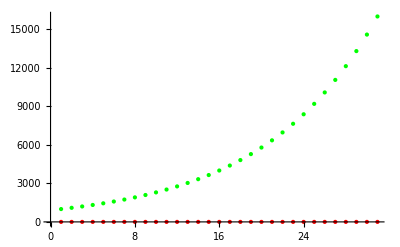

```mathematica
ListPlot[{Table[SimOI[[i]][[2]][[2]][[123]],{i,Length[SimOI]}],Table[SimOI[[i]][[3]][[2]][[123]],{i,Length[SimOI]}]},PlotStyle->{Green,Red}]
```

### Teil 5: Weiterführende Betrachtungen

Wir haben also gesehen dass unser Modell durchaus verwendbar für eine funktionierende Epidemie-Simulation ist. Daher ist es nun vom Interesse das Modell zu erweitern.

#### Verknüpfung mit Nord-Amerika

Seit der Kolonization Amerikas pflegen Europa und Nord-Amerika enge Handelsbeziehungen. In diesem Sinne soll eine Erweiterung des Modells mit Nord-Amerika nun durchgeführt werden. Im großen ganzen und können die aus den vorherigen Teilen erzeugten Algorithmen zur Generierung von Listen und Berechnung des Populationsaustausch schlicht übernommen werden. Um Europa und Nord-Amerika zu verbinden werden Städte mit mehr als 2 x10^6ausgewählt und über Großflughäfen verbunden. Für diesen muss nur noch ein Algorithmus für die Reisebewegung programmiert werden. Um eine zu hohe Komplexität der Algorithmen zur Berechnung der Populationsdynmaik zu vermeiden werden Europa und Nord-Amerika folgend wie ein einziger Kontinent behandelt in dem die CountryData beider Kontinente vereint wird. Im Anschluß kann größtenteils der Listenformalismus der für Europa erstellt wurde übernommen werden. Um zu vermeiden dass Mathematica die Namen von Listen verwechselt werden alle Listen mit dem Kürzel NA (= North American) ergänzt.

```mathematica
NAcountries = Join[CountryData["NorthAmerica"],allcountries]; (*Lädt eine List aller euro-amerikanischen Städte*)
NAlist = Table[{NAcountries[[i]],CountryData[NAcountries[[i]],"Population"]},{i,1,Length[NAcountries]}]; (*Verknüpft Länder mit Populationen*)
NAlist2 = Select[NAlist,#[[2]] >= 2*10^5&]; (*Sortiert Länder mit weniger als 2x10^5 Einwohnern aus*)
selectedNAcountries = Table[NAlist2[[i]][[1]],{i,Length[NAlist2]}]; (*Erstellt eine Liste der vorsortierten Länder*)
Export["NAlist3.txt",Flatten[Table[CityData[{Large,selectedNAcountries[[i]]}],{i,1,Length[selectedNAcountries]}],1]]
NAlist3 =ReadList["NAlist3.txt"];
(*Erstellt eine Liste aller euro-amerikanischen Großstädte*)
```

NAlist3.txt

Vermitteln wir uns eine kurze Übersicht der an der Simulation beteiligten Länder:

```mathematica
NAcountries
```

{Anguilla,AntiguaBarbuda,Aruba,Bahamas,Barbados,Belize,Bermuda,BritishVirginIslands,Canada,CaymanIslands,CostaRica,Cuba,Curacao,Dominica,DominicanRepublic,ElSalvador,Greenland,Grenada,Guadeloupe,Guatemala,Haiti,Honduras,Jamaica,Martinique,Mexico,Montserrat,Nicaragua,Panama,PuertoRico,SaintKittsNevis,SaintLucia,SaintPierreMiquelon,SaintVincentGrenadines,SintMaarten,TrinidadTobago,TurksCaicosIslands,UnitedStates,UnitedStatesVirginIslands,Albania,Andorra,Austria,Belarus,Belgium,BosniaHerzegovina,Bulgaria,Croatia,Cyprus,CzechRepublic,Denmark,Estonia,FaroeIslands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,IsleOfMan,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,SanMarino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,UnitedKingdom,VaticanCity}

Nun gilt es die beteiligten Städte rauszufiltern und Koordinaten für die Visualisierung zu erstellen.

```mathematica
NAlist4 = Table[{NAlist3[[i]][[1]],NAlist3[[i]][[2]],NAlist3[[i]][[3]],CityData[NAlist3[[i]],"Population"]},{i,Length[NAlist3]}]; (*Erzeugt eine Liste mit Elementen nach dem Schema {Stadt,Region,Land,Population}*)
NAlist5 = Sort[Select[NAlist4,#[[4]] >= 2*10^5&]] (*Städte mit mehr als 2x10^5 EW*);
NAlist6 = Sort[Select[NAlist4,#[[4]] >= 1*10^6&]] (*Städte mit mehr als 2x10^6 EW*);
NAlist7 = Sort[Select[NAlist4,#[[4]] >= 2*10^6&]] (*Städte mit mehr als 2x10^6 EW*);
NAcountries = Sort[DeleteDuplicates[Table[NAlist5[[i]][[3]],{i,Length[NAlist5]}]]]; (*Erzeugt Liste aller beteiligten eu-am. Länder*)
NAcities = Table[{NAlist5[[i]][[1]],NAlist5[[i]][[2]],NAlist5[[i]][[3]]},{i,Length[NAlist5]}]; (*Erzeugt Liste aller beteiligten eu-am. Städte*)
NApop = Table[NAlist5[[i]][[4]],{i,Length[NAlist5]}]; (*Erzeugt Liste aller zu den Städten gehörigen eu-am. Populationen*)Print["An der folgenden Simulation sind im euro-amerikanischen Raum " ,Style[Length[NAcountries],Red]," Länder und ", Style[Length[NAcities],Red], " Städte beteiligt."]
NAcoords = Table[{NAcities[[i]],CityData[{NAcities[[i]][[1]],NAcities[[i]][[2]],NAcities[[i]][[3]]},"Coordinates"]},{i,Length[NAcities]}] ;
(*Liste der Koordinaten in der Form {{Stadt,Region,Land},{Koordinaten}}*)
```

An der folgenden Simulation sind im euro-amerikanischen Raum 51 Länder und 466 Städte beteiligt.

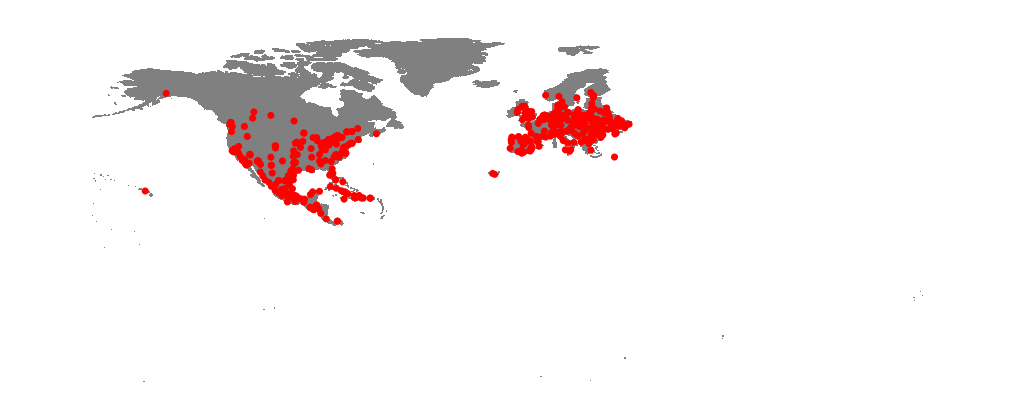

```mathematica
NAmap1 =Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["UnitedStates","FullPolygon"]},{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@NAcoords,2]]}}]] (*Übersicht über die in der Simulation beteiligten Städte*)
```

Folgend wird die Liste aller Landverbindungen erzeugt:

```mathematica
NAland0 = Table[{NAcities[[i]],Select[Table[{Delete[NAcoords,i][[j]][[1]],GeoDistance[NAcoords[[i]][[2]],Delete[NAcoords,i][[j]][[2]]]},{j,Length[NAcoords]-1}],#[[2]] <= 500*10^3&]},{i,Length[NAcoords]}];(*Liste aller Landverbindung in der Form {Stadt,{{Nachbarstadt1,Distanz1},...,}}*)
Export["NAland.txt",NAland0]
NAland = ReadList["NAland.txt"];
NAlcon = Flatten[Table[Table[{Reverse[CityData[NAland[[i]][[1]],"Coordinates"]],Reverse[CityData[NAland[[i]][[2]][[j]][[1]],"Coordinates"]]},{j,Length[NAland[[i]][[2]]]}],{i,Length[land]}],1];(*Liste aller Landverbindungen in Form von {Ausgangsstadt-Koordinate,Nachbarstadt-Koordinate}; nur relevant für die Übersichtskarte*)
```

NAland.txt

Ein Plot aller Landverbindungen liefert uns:

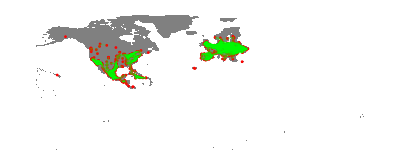

```mathematica
NAmap2 =Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["UnitedStates","FullPolygon"]},{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@NAcoords,2]]},{Red,PointSize[0.005]},{Green,Opacity[0.2],Line[NAlcon]}}]]
```

Bei den Luftverbindungen gibt es eine  Problematik die der klassische Listenformalismus nicht berücksichtigt. Städte mit mehr als 1 x10^6 würden auch transkontinental verbindet werden, obwohl nur Städte mit mehr als 2 x10^6 über Transkontinentalverbindungen verfügen sollen. Daher muss die Liste aller Städte mit Flughäfen (NAlist6) nach europäischen und nord-amerikanischen Städten gefiltert werden.

```mathematica
contfilter =Table[{NAlist6[[i]][[1]],NAlist6[[i]][[2]],NAlist6[[i]][[3]],CountryData[NAlist6[[i]][[3]],"Continent"]},{i,Length[NAlist6]}];EUairports = Select[contfilter,#[[4]]=="Europe"&]; (*Liste aller europäischen Städte mit Interkontinental-Flughafen*)
NAairports = Select[contfilter,#[[4]]=="NorthAmerica"&];(*Liste aller nord-amerikanischen Städte mit Interkontinental-Flughafen*)
```

Getrenntes anwenden des Permutations-Befehls 2ter-Ordnung mit anschließender Wiedervereinigung der Städte liefert uns nun die korrekte Struktur der Luftverbindungen, welche wir in der Variablen NAair speichern.

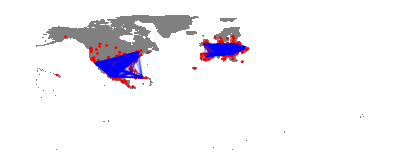

```mathematica
NAair = Join[Permutations[EUairports,{2}],Permutations[NAairports,{2}]]; (*Liste aller Städte mit interkontinentalen Flugverbindungen*)
NAaircitycoords =Table[{Reverse[CityData[{NAair[[i]][[1]][[1]],NAair[[i]][[1]][[2]],NAair[[i]][[1]][[3]]},"Coordinates"]],Reverse[CityData[{NAair[[i]][[2]][[1]],NAair[[i]][[2]][[2]],NAair[[i]][[2]][[3]]},"Coordinates"]]},{i,Length[NAair]}]; 
NAmap3 = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["UnitedStates","FullPolygon"]},{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@NAcoords,2]]},{Blue,Opacity[0.2],Line[NAaircitycoords]}}]]  (*Darstellung aller intekontinentalen Luftverbindungen*)
```

Neu in dieser Simulation ist nun die Verbindung von nord-amerikanischen mit europäischen Städten über Großflughäfen. Dies wird in folgender Inputzeile durchgeführt:

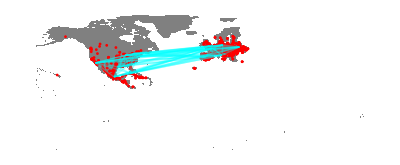

```mathematica
bigair = Permutations[NAlist7,{2}] ;(*Liste der transkontinentalen Flugverbindungen*)
bigaircitycoords =Table[{Reverse[CityData[{bigair[[i]][[1]][[1]],bigair[[i]][[1]][[2]],bigair[[i]][[1]][[3]]},"Coordinates"]],Reverse[CityData[{bigair[[i]][[2]][[1]],bigair[[i]][[2]][[2]],bigair[[i]][[2]][[3]]},"Coordinates"]]},{i,Length[bigair]}]; (*Koordinaten der Städte mit Flugverbindungen; nur relevant für Übersichtskarte*)
continentalmap = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["UnitedStates","FullPolygon"]},{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@NAcoords,2]]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@coords,2]]},{Cyan,Opacity[0.2],Line[bigaircitycoords]}}]]  (*Darstellung aller kontinentalen Luftverbindungen*)
NAmap4 = Show[Graphics[{{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["UnitedStates","FullPolygon"]},{CountryData["Spain","FullPolygon"]}]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@NAcoords,2]]},{Red,PointSize[0.005],
Point[Reverse[#[[2]]&/@coords,2]]},{Green,Opacity[0.2],Line[lcon]},{Green,Opacity[0.2],Line[NAlcon]},{Blue,Opacity[0.2],Line[aircitycoords]},{Blue,Opacity[0.2],Line[NAaircitycoords]},{Cyan,Opacity[0.2],Line[bigaircitycoords]}}]]; (*Darstellung aller Verbindungen. Nur relevant für Übersicht im nächsten Teil*)
```

Verschaffen wir uns nun eine Übersicht über das neue Werkzeug:

```mathematica
NAcountries; (*Liste aller an der Simulation beteiligten n.a.Länder*)
NAcities; (*Liste aller an der Simulation beteiligten n.a. Städte*)
NApop; (*Liste der zu den n.a.Städten zugehörigen Populationszahlen*)
NAland; (*Liste der zu den n.a.Städten zugehörigen Landverbindungen*)
NAair; (*Liste der zu den n.a. Städten zugehörigen Luftverbindungen*)
bigair; (*Liste aller Kontinentalverbindungen zwischen Europa und Nordamerika*)
GraphicsGrid[{{NAmap1,NAmap2,NAmap3,continentalmap}}] (*Übersicht über die Europa und seine Verkehrsbindungen*)
```

-Graphics-

Nun gilt es einen Algorithmus zu programmieren der den kontinentalen Populationsaustausch berechnet.

Für die interkontinentale Populationsdynamik können ein Großteil der Module aus Teil 2 und Teil 3 der Erstellung des Modells direkt übernommen werden. Lediglich für transkontinentale Reisebewegung ist ein neues Modul nötig, welches folgend als travelBigAir bezeichnet wird. Das Modul funktioniert jedoch in grundlegender Analogie zu dem travelAir-Modul.

```mathematica
travelBigAir[{sus0_,inf0_,rec0_},i_]:=Module[{ω,bigair2,bigair3,listpos,change0,change1,change2,change3,change4,trsus,trinf,trrec,popnow,omegas},
bigair2=Table[{{bigair[[j]][[1]][[1]],bigair[[j]][[1]][[2]],bigair[[j]][[1]][[3]]},{bigair[[j]][[2]][[1]],bigair[[j]][[2]][[2]],bigair[[j]][[2]][[3]]}},{j,Length[bigair]}] ;(*Erzeugt Liste der Luftverbindungen ohne Bevölkerungszahlen*)
bigair3 = Select[bigair2,(#[[1]]==NAcities[[i]])&] ;(*Liste aller Nachbarstädte*)
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
ω[z_] := (2*pt)/(Length[bigair3]+Length[bigair3]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus=sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec =rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)listpos = Table[Position[NAcities,bigair3[[j]][[2]]][[1]],{j,Length[bigair3]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}]; (*Erstellt eine leere Liste welche als Speicher für die berechneten Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{1,1,1}ω[j]],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{trsus,trinf,trrec}];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = Table[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]}*omegas[[j]][[1]],{j,1,Length[change2]}];
change4 = ReplacePart[change3, {i} -> -Sum[{change3[[j]][[1]],change3[[j]][[2]],change3[[j]][[3]]},{j,Length[change2]}]];
If[Length[change4]==0,Return[0],Return[change4]
];
];
```

```mathematica
travelBigAirAll[{sus0_,rec0_,inf0_}] := Module[{a,sus,inf,rec},
a= Sum[travelBigAir[{sus0,rec0,inf0},j],{j,1,Length[sus0[[2]]]}];
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};
Return[{sus,inf,rec}]
];
```

Anpassung der Module aus Teil 2 und Teil 3 der Modellierung:

```mathematica
travelNALand[{sus0_,inf0_,rec0_},i_]:=Module[{ω,trsus,trinf,trrec,land2,listpos,change0,change1,change2,change3,change4,popnow,omegas},
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
ω[z_] := (2*pt)/(Length[NAland[[i]][[2]]]+Length[NAland[[z]][[2]]]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus= sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)land2 =Table[NAland[[i]][[2]][[j]][[1]],{j,Length[NAland[[i]][[2]]]}]; (*Liste aller Nachbarstädte, ohne Entfernung zur Ausgangsstadt*)
listpos = Table[Position[NAcities,land2[[j]]][[1]],{j,Length[land2]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}];
omegas = Sum[ReplacePart[change0,listpos[[j]]->{1,1,1}ω[j]],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{trsus,trinf,trrec}];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = Table[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]}*omegas[[j]][[1]],{j,1,Length[change2]}];
change4 = ReplacePart[change3, {i} -> -Sum[{change3[[j]][[1]],change3[[j]][[2]],change3[[j]][[3]]},{j,Length[change2]}]];
If[Length[change4]==0,Return[0],Return[change4]
];
];
```

```mathematica
travelNAAir[{sus0_,inf0_,rec0_},i_]:=Module[{ω,air2,air3,listpos,change0,change1,change2,trsus,trinf,trrec,change3,change4,popnow,omegas},
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
air2=Table[{{NAair[[j]][[1]][[1]],NAair[[j]][[1]][[2]],NAair[[j]][[1]][[3]]},{NAair[[j]][[2]][[1]],NAair[[j]][[2]][[2]],NAair[[j]][[2]][[3]]}},{j,Length[NAair]}] ;(*Erzeugt Liste der Luftverbindungen ohne Bevölkerungszahlen*)
air3 = Select[air2,(#[[1]]==NAcities[[i]])&] ;(*Liste aller Nachbarstädte*)
ω[z_] := (2*pt)/(Length[air3]+Length[air3]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus=sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)
listpos = Table[Position[NAcities,air3[[j]][[2]]][[1]],{j,Length[air3]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}]; (*Erstellt eine leere Liste welche als Speicher für die berechneten Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{1,1,1}ω[j]],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{trsus,trinf,trrec}];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = Table[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]}*omegas[[j]][[1]],{j,1,Length[change2]}];
change4 = ReplacePart[change3, {i} -> -Sum[{change3[[j]][[1]],change3[[j]][[2]],change3[[j]][[3]]},{j,Length[change2]}]];
If[Length[change4]==0,Return[0],Return[change4]
];
];
```

```mathematica
travelNALandAll[{sus01_,inf01_,rec01_}] := Module[{b,sus,inf,rec},
b= Sum[travelNALand[{sus01,inf01,rec01},j],{j,1,Length[NAcities]}];
sus = {0,Table[b[[i]][[1]],{i,Length[sus01[[2]]]}]};
inf = {0,Table[b[[i]][[2]],{i,Length[sus01[[2]]]}]};
rec = {0,Table[b[[i]][[3]],{i,Length[sus01[[2]]]}]};
Return[{sus,inf,rec}]
];

travelNAAirAll[{sus0_,rec0_,inf0_}] := Module[{a,sus,inf,rec},
a= Sum[travelNAAir[{sus0,rec0,inf0},j],{j,1,Length[sus0[[2]]]}];
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};
Return[{sus,inf,rec}]
];
```

Nun muss lediglich der Simulate-Befehl und der Visualize-Befehl angepasst werden. Wir benutzen wegen den für diese Simulation geringen numerischen Unterschieden den schnelleren Euler-Algorithmus:

```mathematica
NASimulateEuler[{sus0_,inf0_,rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,susS5,infS5,recS5,cont,i},
i=1;
cont ={};
cont =Append[cont,{sus0,inf0,rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelNALandAll[{susS1,infS1,recS1}];
{susS3,infS3,recS3}={susS2,infS2,recS2}+travelNAAirAll[{susS2,infS2,recS2}];
{susS4,infS4,recS4} = {susS3,infS3,recS3}+travelBigAirAll[{susS3,infS3,recS3}];
{susS5,infS5,recS5}=InfectEulAll[{susS4,infS4,recS4}];
{sus,inf,rec}={{i,susS5},{i,infS5},{i,recS5}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

```mathematica
NAtmc[SimInput_,i_,j_] := Module[{Sim,SumPop,SusPop,InfPop,RecPop},
Clear[Sim];
Sim = SimInput;
SumPop:=Sim[[j]][[1]][[2]][[i]]+Sim[[1]][[2]][[2]][[i]]+Sim[[1]][[3]][[2]][[i]];
SusPop :=Sim[[j]][[1]][[2]][[i]];
InfPop :=Sim[[j]][[2]][[2]][[i]];
RecPop := Sim[[j]][[3]][[2]][[i]];
Return[{RGBColor[HeavisideTheta[SusPop-0.01]-HeavisideTheta[InfPop-0.01],HeavisideTheta[InfPop-0.01]*Log[E+InfPop]/Log[E+InfPop+RecPop],Log[E+RecPop]/Log[E+InfPop+RecPop]*HeavisideTheta[InfPop-0.01]],PointSize[0.005+0.005*HeavisideTheta[InfPop-0.01]],Point[Reverse[NAcoords[[i]][[2]]]]}]
];
```

```mathematica
NAVisualize[SimInput_]:=Module[{colorlist,colorlist2},
colorlist = Table[Table[NAtmc[SimInput,i,j],{j,1,Length[SimInput]}] ,{i,Length[SimInput[[1]][[1]][[2]]]}];
colorlist2 =Transpose[colorlist];
Manipulate[Graphics[{Background->LightGray,{Gray,Join[CountryData[#,"Polygon"]&/@CountryData["Europe"],{CountryData["Spain","FullPolygon"]},CountryData[#,"Polygon"]&/@CountryData["NorthAmerica"],{CountryData["UnitedStates","FullPolygon"]}]},colorlist2[[k]]}],{k,1,Length[SimInput],1}]
];
```

Lassen wir nun eine Test-Simulation durchlaufen:

```mathematica
pt = 0.2;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate derKrankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
```

Wir setzen wieder 1000 Infizierte Menschen in London rein. Die Listenposition in NAcities  lässt sich recht einfach mit Hilfe des CityData- und des Position-Befehls finden:

```mathematica
Position[NAcities,CityData["London"][[1]]]
```

{{226}}

Die Anfangszahlen der Bevölkerungspopulationen sind dann:

```mathematica
NAsus1 = {0,NApop};
NAinf1= {0,ReplacePart[Table[0,{i,Length[NApop]}],{224}->1000]};
NArec1 = {0,Table[0,{i,Length[NApop]}]};
NAsir0 = {NAsus1,NAinf1,NArec1};
```

```mathematica
SimEUAM=NASimulateEuler[NAsir0,30];
```

```mathematica
SimEUAM[[31]][[2]]
```

{30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,4,1,1,0,0,0,3,0,4,0,1,0,0,0,6,2,0,8,2,0,0,0,0,0,0,19,0,0,0,30,1,22,7,38,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,5,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,4,0,12,0,0,0,0,0,0,10,0,1,10,2,2,0,0,2,0,0,0,1,0,0,0,4,0,5,0,26,0,0,4,11,0,0,0,0,0,0,0,2,0,44,0,0,0,0,0,0,0,0,0,21,0,0,0,0,0,0,3,12,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7,7,0,8,0,0,0,3,29,0,0,0,0,7,8,2,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,61,10,28,0,0,0,0,0,0,0,0,1,19,0,0,1,6,0,8,3,0,0,0,0,0,0,6,0,0,6,0,0,0,0,0,0,0,0,0,15,0,0,12,0,0,0,1,0,0,0,0,0,0,59,1,0,0,0,19,0,0,0,0,0,0,0,31,0,0,0,0,0,0,0,19,0,0,1,0,4,0,0,9,0,0,9,0,0,0,0,22,0,0,0,0,25,0,0,0,0,0,0,0,0,0,0,0,0,4,19,3,0,0,0,7,0,0,0,0,0,0,0,0,0,0,146,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36,0,0,0,0,0,0,0,4,31,0,6,0,0,0,0,0,0,9,30,0,0,1,0,0,0,0,0,0,0,0,0,0,0,12,29,0,0,0,0,0,0,0,4,0,31,0,0,39,0,0,1,0,0,0,0,0,37,0,44,0,0,22,0,0,0,0,0,0,0,0,6,0,0,2,0,0,0,0,6,3,0,0,16,0,0,0,0,31}}

```mathematica
NAVisualize[SimEUAM]
```

#### Spanische Grippe mit der Nord-Amerika-Erweiterung

Das nun erstellte Modell eröffnet uns nun die Möglichkeit es zu versuchen die in der Einleitung erwähnte Spanische Grippe nachzusimulieren.

Das Epizentrum der Pandemie wird auf den US-amerikanischen Bundeststaat Kansas eingeschätzt. Durch umsortieren der NAcities-Liste finden wir mit Hilfe des Position-Befehls eine Stadt die Kansas liegt.

```mathematica
Position[Table[NAcities[[i]][[2]],{i,1,Length[NAcities]}],"Kansas"]
NAcities[[446]]
```

{{451}}

{VirginiaBeach,Virginia,UnitedStates}

Es handelt es sich hier ersichtlicherweise um Wichita.

```mathematica
NA1918sus1 = {0,NApop};
NA1918inf1= {0,ReplacePart[Table[0,{i,Length[NApop]}],{446}->10000]};
NA1918rec1 = {0,Table[0,{i,Length[NApop]}]};
NA1918sir0 = {NA1918sus1,NA1918inf1,NA1918rec1};
```

Die Spanische Gruppe wurde von US-Soldaten auch als Three-Day-Fever bezeichnet aufgrund ihrer kurzen Krankheitsdauer. Realistischer sind wahrscheinlich ~5 Tage. Da die Erholungsrate ν das Inverse der Infektionsdauer darstellt wollen wir folgend ν ≡ 0.2 setzen. Die Spanische Gruppe war eine tödlich verlaufende Erkrankung wobei die Mortalität Infizierter zwischen 10 und 20% beträgt. Wir führen daher eine Influenzsterblichkeitsrate τ ein mit τ ≡ 0.03 1 / Tag. Wir modifizieren dementsprechend unsere DGLs:

d/dt s[t] = -β*(s[t]*i[t])/(s[t]+i[t]+r[t])-μ*s[t]+μ*(s[t]+i[t]+r[t])
d/dt i[t] = β*(s[t]*i[t])/(s[t]+i[t]+r[t])-ν*i[t]-μ*i[t]-τ*i[t]
d/dt r[t] =ν*i[t]-μ*r[t]

Die Geburtenrate wird oft in Einheit (10^3 Personen x (Jahr))^-1 angegeben. Für diese findet sich für die USA eine Angabe von 29.5 für das Jahr 1915. Teilen wir diese Zahl durch 1000 und 365 so erhalten wir eine Geburtenrate von 8 x10^-5. Wir nehmen an, dass diese auch in guter Näherung für Europa gilt. Für die Infektionsrate sind leider keine Daten für Nord-Amerika oder Europa auffindbar. Daher wird im folgenden der Parameter β ≡ 0.1 schlicht übernommen.  Auch für die Reisewahrscheinlichkeit sind leider keine genauere Schätzungen bekannt. 

Quelle: 
http://en.wikipedia.org/wiki/1918_flu_pandemic
http://de.wikipedia.org/wiki/Spanische_Grippe
http://www.infoplease.com/ipa/A0005067.html

```mathematica
pt = 0.01;(*Reisewahrscheinlichkeit*)
beta  = 0.1;(*Infektionsrate der Krankheit*)
nu = 0.2;(*Erholungsrate der Krankheit*)
mu = 8*10^-5;(*Geburten-/Sterberate*)
tau = 0.15; (*Influenzsterblichkeitsrate*)
```

Nun muss lediglich das Lösungsverfahren entsprechend der Modifizierung der DGLs modifiziert werden:

```mathematica
Infect1918Euler[{NA1918sus0_,NA1918inf0_,NA1918rec0_},j_] := Module[{fs,fi,fr,Δ,t},
Clear[i];
s[0]=NA1918sus0[[2]][[j]];
i[0]=NA1918inf0[[2]][[j]];
r[0]=NA1918rec0[[2]][[j]];
fs[t_,Δ_]=s[t]+Δ*(-beta*s[t]*i[t]/(s[t]+i[t]+r[t])-mu*s[t]+mu*(s[t]+i[t]+r[t]));
fi[t_,Δ_]=i[t]+Δ*(beta*i[t]*s[t]/(s[t]+i[t]+r[t])-nu*i[t]-mu*i[t]-tau*i[t]);
fr[t_,Δ_]=r[t]+Δ*(nu*i[t]-mu*r[t]);
Return[Round[{fs[t,Δ],fi[t,Δ],fr[t,Δ]}/.{t->0,Δ->1}]]
];

Infect1918EulAll[sir0_]:=Module[{susEul,infEul,recEul,a},
a= Table[Infect1918Euler[sir0,j],{j,1,Length[sir0[[1]][[2]]]}];
susEul = Table[a[[j]][[1]],{j,1,Length[sir0[[1]][[2]]]}]; 
infEul = Table[a[[j]][[2]],{j,1,Length[sir0[[1]][[2]]]}]; 
recEul = Table[a[[j]][[3]],{j,1,Length[sir0[[1]][[2]]]}]; 
Return[{susEul,infEul,recEul}]
];
```

Und das Simulator-Modul angepasst werden:

```mathematica
NA1918SimulateEuler[{NA1918sus0_,NA1918inf0_,NA1918rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,susS5,infS5,recS5,cont,i},
i=1;
cont ={};
cont =Append[cont,{NA1918sus0,NA1918inf0,NA1918rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelNALandAll[{susS1,infS1,recS1}];
{susS3,infS3,recS3}={susS2,infS2,recS2}+travelNAAirAll[{susS2,infS2,recS2}];
{susS4,infS4,recS4} = {susS3,infS3,recS3}+travelBigAirAll[{susS3,infS3,recS3}];
{susS5,infS5,recS5}=Infect1918EulAll[{susS4,infS4,recS4}];
{sus,inf,rec}={{i,susS5},{i,infS5},{i,recS5}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

Jetzt kann die Simulation beginnen:

```mathematica
Sim1918 = NA1918SimulateEuler[NA1918sir0,30];
```

Offensichtlich sind nach 30 Tagen die Zahlen der Infizierten stark gesunken:

```mathematica
Sim1918[[31]][[2]]
```

{30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}

Betrachten wir die Simulations-Ergebnisse mit dem NAVisualize-Befehl:

```mathematica
NAVisualize[Sim1918]
```

Nachgewiesen wurde die Spanische Grippe nach Auftreten in Kansas zuerst in Frankreich und dann an der nord-amerikanischen Eastcoast in Boston. Wie sich zeigt, lässt sich innerhalb der 30 Tage leider keine signifikante Ausbreitung der Krankheit feststellen. Sie breitet sich lediglich leicht im amerikanischen Midwest aus. Hinderlich ist möglicherweise die Sterberate welche dazu führt, dass letztendlich die Infiziertenzahlen und somit auch Infektionquellen gedrückt werden. Schauen wir uns nun einen Plot der Infiziertenzahlen in Wichitas an:

```mathematica
ListPlot[Table[Sim1918[[i]][[2]][[2]][[446]],{i,1,Length[Sim1918]}]]
```

-Graphics-

Die Zahl der Infizierten nimmt sehr schnell sehr stark ab was aufgrund der Mortalität zu erwarten ist.

```mathematica
ListPlot[Table[Sim1918[[i]][[3]][[2]][[446]],{i,1,Length[Sim1918]}]]
```

-Graphics-

Im gleichem Maße steigen die Zahl der Erholten stark an.

```mathematica
ListPlot[Table[Sim1918[[i]][[1]][[2]][[446]],{i,1,Length[Sim1918]}]]
```

-Graphics-

Die Zahl der Uninfizierten steigt anfangs stark ab, stellt  sich jedoch letzlich auf konstantes Level.

Wie ist also nun der Versuch der Simulation der Spanischen Grippe zu bewerten? Zunächst einmal ist zusagen, dass viele Modellparameter leider unbekannt sind und daher die Simulation sich nicht wirklich an der Realität orientiert. Auf der anderen Seite wurden für die Simulation Daten bezogen welche für das 21ste Jahrhundert gelten. So stimmen viele Einwohnerzahlen nicht und Luftverkehr gab es im diesen Sinne auch nicht. Zwar gab es reges transkontinentales Verkehrsaufkommen durch die Schifffahrt, diese lässt sich allerdings nicht so einfach modellieren wie der Luftverkehr. Die Schifffahrt ist stark an geografische Gegebenheiten gebunden während die Luftfahrt im Prinzip "jegliches Hindernis" überfliegt. Hafenstädte wären daher für einen transkontinentalen Populationsaustausch basierend auf Schifffahrt von höherer Bedeutung als sie im derzeitigen Modell sind. Daher ist das ausgearbeitete Modell als gänzlich ungeeignet für die Simulation der Ausbreitung der Spanischen Grippe zu bewerten.

Um zu Testzwecken nun trotzdem eine Ausbreitung auch in Europa zu erhalten wird die Influenz bedingte Sterblichkeit auf 0.05 gesetzt und die auf 0,1 und die Infektionsrate auf 0,5. Reine Modifkation der Reisewahrscheinlichkeit bewirkt lediglich eine weitere Ausbreitung innerhalb der USA, welche aber aufgrund der hohen Sterblichkeitsrate schnell zum Stillstand kommt. Deswegen muss diese verringert werden. Da aber nur Städte mit mehr als 2 Milllionen Einwohnern über Verbindungen zu Europa verfügen ist es zusätzlich sinnvoll die Infektionsrate hochzudrehen um innerhalb von 30 Simulationsschritten auf das gewünschte Ergebnis zu kommen.

```mathematica
pt = 0.1;(*Reisewahrscheinlichkeit*)
beta  = 0.5;(*Infektionsrate der Krankheit*)
nu = 0.2;(*Erholungsrate der Krankheit*)
mu = 8*10^-5;(*Geburten-/Sterberate*)
tau = 0.05; (*Influenzsterblichkeitsrate*)
```

```mathematica
Sim19182 = NA1918SimulateEuler[NA1918sir0,30];
NAVisualize[Sim19182]
Sim19182[[31]][[2]]
```

{30,{15,151,3,374,83,25,36,26,125,0,26,173,5,163,10959,0,13446,20,18058,0,398,11,5,250,48660,11,126,20,147,46,4,153,0,2403,5,26,26,64,3761,380,64,0,38,117,34,37549,43,5,3437,9,9,20,14,61,31,44,551,229,289,446,25938,0,12,45,0,62,1,0,95,82,0,651,236,72,83143,41,45,71,119,102257,8962,176,1753,51,0,436,8998,35493,26,1542,204,74,0,20827,8,14,272,477,62,9,846,894,38,20,7998,17,156,0,30,144,13013,75,567,9,45,36,145,109,590,71673,50,2895,5,0,159,330,65,1273,45,0,99,56076,56,6897,493,91,50,12,654,14,729,8246,36,7,94,876,226,107,92,265,7,572,413,143,2,83,9,45923,14723,505,64,0,0,37,367,6539,43,20149,0,703,139,183,50,30,0,12,17489,9,107,8176,1240,533,486,41,808,11609,39416,10392,26,44,53,8,455,34,45,34,18,11720,45,24,44,13602,14,17,86,183,72,415,578,0,53,577,5480,53,47,30,13805,25238,16,99,5,25,19,53,22,6964,6497,1202,712,14116,13,597,5868,476,70,37,8,56,47,93,428,11019,51,116,12,46,47,0,34,74,36,10066,12,780,416,2189,0,225,67,886,25282,424,182,2146,62,456,14204,2,97,79,11540,4520,6,15423,2242,221,558,37,92,34,52,28,4672,36,1068,59327,481,493043,3947,188,1327,0,63747,45010,774,37,904,39,17,1210,90,5,314,203,11,14,323,0,24,10120,82,74580,2029,50,59,7,0,644,6591,173,72581,5242,55619,894,25,4,134,66,242,0,52,53,238,9,19236,4094,626,22,54279,107,124,27,605,111489,1,1846,82,47317,10391,111,11,9,1081,52,2026,448,10702,724,12391,23,144,0,146,1267,0,342,163,0,0,626,0,1171,246,0,821,16,6457,11,0,338,0,16,89,34,18,6,701,1818,34,76,0,0,0,37,26,54,39,46,0,29,0,547,0,971,0,999,886,131,125,1,14678,27,12,1461,1350,9982,808,726,37810,568,31,6,50,1802,193,31,50,2109,73,61,392,0,9,14263,64,757,34,0,2125,96,114,74,7,8,70,80361,18,72,228,95974,24,133,13696,0,74114,62,46,89,475,1463,12,2446,117,114,60,83}}

#### Maßnahmen zur Eindämmung der Epidemie

Außgehend von dem Versuch die Spanische Grippe zu simulieren erweitern wir unsere Module nun mit Epidemieeindämmungsmaßnahmen. Dabei liese es sich zu einem an Quarantänemaßnahmen denken und zum anderen an eine Impfkampagne. Bei einer Impfung handelt es sich um eine Präventivmaßnahme welche zu einer Immunisierung gefährdeter Menschen führen soll. Der Einbau dieser erfolgt über die Modifkation der Differentialgleichungen:

d/dt s[t] = -β*(s[t]*i[t])/(s[t]+i[t]+r[t])-μ*s[t]+μ*(s[t]+i[t]+r[t])-ι*s[t] * w[avac,s[t],i[t],r[t]] 
d/dt i[t] = β*(s[t]*i[t])/(s[t]+i[t]+r[t])-ν*i[t]-μ*i[t]-τ*i[t]
d/dt r[t] =ν*i[t]-μ*r[t]+ι*s[t] * wvacc[avacc,s[t],i[t],r[t]]

Die wesentlich Modifkation in den DGLs ist der Einbau der Impfrate ι. Diese Führt dazu, dass Menschen von den Susceptibles direkt in die Recovered-Gruppe überführt werden uns somit nicht mehr empfänglich für eine Infektion sind. Da allerdings Impfkampagnen nicht mutwillig durchgeführt werden, sondern erst einer gewissen Aufmerksam bzgl. einer Krankheit vorraussetzen, muss ein Wichtungsfaktor w[avacc,s[t],i[t],r[t] eingebaut werden, welcher den prozentuellen Anteil der Infizierten innerhalb einer Stadtbevölkerung misst. Überschreitet dieser den global vorgegebenen Wert avacc, so wird wir die Impfkampagne gestartet und 
w ≡ 1 gesetzt. Ansonsten ist w ≡ 0 und die Impfkampagne bleibt aus.

Im Gegensatz zur Impfkampagne stellen Quarantänemaßnahmen Notfallaktionen dar. Sie sollen vor allem verhindern dass eine Krankheit Stadtgrenzen überschreitet und andere Städte infiziert werden. Implementieren lassen sich Quarantänemaßnahmen, indem man die Reisewahrscheinlichkeit um zusätzliche Wichtungsfaktoren erweitert. Für die k-te Stadt gilt dabei dann und eine beliebige Nachbarstadt l gilt dann:

P_T*wqnt[aqnt,s_k[t],i_k[t],r_k[t]]*wqnt[aqnt,s_l[t],i_l[t],r_l[t]]

Es wurde ein Wichtungsfaktor wqnt nun eingeführt. Dieser funktioniert prinzipiell ähnlich wie der Wichtungsfaktor für die Impfkampagne. Überschreitet der prozentuale Anteil der Infizierten innerhalb einer n-ten Stadt den global vorgegebenen Wert aqnt, so wird die der Wichtungsfaktor nun wqnt ≡ 0 gesetzt. Ansonsten ist der Wichtungsfaktor wqnt ≡ 1. Der neue Wichtungsfaktor schaltet also prinzipiell je nach prozentualen Anteil die Reisewahrscheinlichkeit komplett ab oder an. Um ausgehend von einer k-ten Stadt zugewährleisten, dass mit einer vorgebenen unter Quarantäne stehende Nachbarstadt l_0 nun keine Menschen ausgetauscht werden, muss die Reisewahrscheinlichkeits zusätzlich mit einem Wichtungsfaktoren bezogen auf l beliebige Nachbarstädte multipliziert werden. 

Definieren wir also erstmal unsere Parameter:

```mathematica
pt = 0.1;(*Reisewahrscheinlichkeit*)
beta  = 0.5;(*Infektionsrate der Krankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
tau = 0; (*Mortalität der Krankheit*)

iota = 0.05;(*Impfrate*)
avacc = 0.10; (*Prozentualer Anteil an Infizierten um Impfkampagne zu starten*)
aqnt = 0.20; (*Prozentualer Anteil an Infizierten um Quarantänemaßnahmen zu starten*)
```

Jegliche neuen Module und Funktionen erhalten nun das Kürzel MVQ, welches für Mortality, Vaccination, Quarantine steht, also die in dem folgenden Modell wesentlichen Features. Modifizieren wir nun unsere DGLs und die damit verbundene Lösungsmtehode um die Impfrate mit zu berücksichtigen:

```mathematica
InfectMVQEuler[{NAsus0_,NAinf0_,NArec0_},j_] := Module[{fs,fi,fr,Δ,t,wvacc},
Clear[i];
s[0]=NAsus0[[2]][[j]];
i[0]=NAinf0[[2]][[j]];
r[0]=NArec0[[2]][[j]];
wvacc = If[i[0]/(s[0]+i[0]+r[0])<avacc,0,1];
fs[t_,Δ_]=s[t]+Δ*(-beta*s[t]*i[t]/(s[t]+i[t]+r[t])-mu*s[t]+mu*(s[t]+i[t]+r[t])-iota*s[t]*wvacc);
fi[t_,Δ_]=i[t]+Δ*(beta*i[t]*s[t]/(s[t]+i[t]+r[t])-nu*i[t]-mu*i[t]-tau*i[t]);
fr[t_,Δ_]=r[t]+Δ*(nu*i[t]-mu*r[t]+iota*s[t]*wvacc);
Return[Round[{fs[t,Δ],fi[t,Δ],fr[t,Δ]}/.{t->0,Δ->1}]]
];

InfectMVQEulAll[sir0_]:=Module[{susEul,infEul,recEul,a},
a= Table[InfectMVQEuler[sir0,j],{j,1,Length[sir0[[1]][[2]]]}];
susEul = Table[a[[j]][[1]],{j,1,Length[sir0[[1]][[2]]]}]; 
infEul = Table[a[[j]][[2]],{j,1,Length[sir0[[1]][[2]]]}]; 
recEul = Table[a[[j]][[3]],{j,1,Length[sir0[[1]][[2]]]}]; 
Return[{susEul,infEul,recEul}]
];
```

Und nun die Berechung des Reisevekehrs. Beginnend mit dem transkontinentalen Reisevekehr:

```mathematica
travelBigAirMVQ[{sus0_,inf0_,rec0_},i_]:=Module[{ω,bigair2,bigair3,listpos,change0,change1,change2,change3,trsus,trinf,trrec,popnow, wqnt,omegas},
bigair2=Table[{{bigair[[j]][[1]][[1]],bigair[[j]][[1]][[2]],bigair[[j]][[1]][[3]]},{bigair[[j]][[2]][[1]],bigair[[j]][[2]][[2]],bigair[[j]][[2]][[3]]}},{j,Length[bigair]}] ;(*Erzeugt Liste der Luftverbindungen ohne Bevölkerungszahlen*)
bigair3 = Select[bigair2,(#[[1]]==NAcities[[i]])&] ;(*Liste aller Nachbarstädte*)
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
wqnt[k_] := If[(inf0[[2]][[k]]/popnow[k])<aqnt,1,0];
ω[z_] := (2*pt)/(Length[bigair3]+Length[bigair3]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus=sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)listpos = Table[Position[NAcities,bigair3[[j]][[2]]][[1]],{j,Length[bigair3]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}]; (*Erstellt eine leere Liste welche als Speicher für die berechneten Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{ω[j],ω[j],ω[j]}],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{Round[trsus*omegas[[j]][[1]]],Round[trinf*omegas[[j]][[2]]],Round[trrec*omegas[[j]][[3]]]}*wqnt[j]*wqnt[i]];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = ReplacePart[change2, {i} -> -Sum[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]},{j,Length[change2]}]];
Return[change3];
];

travelBigAirAllMVQ[{sus0_,rec0_,inf0_}] := Module[{a,sus,inf,rec},
a= Sum[travelBigAirMVQ[{sus0,rec0,inf0},j],{j,1,Length[sus0[[2]]]}];
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};
Return[{sus,inf,rec}]
];
```

Der interkontinentale Luftreiseverkehr:

```mathematica
travelAirMVQ[{sus0_,inf0_,rec0_},i_]:=Module[{ω,air2,air3,listpos,change0,change1,change2,trsus,trinf,trrec,change3,popnow,wqnt,omegas},
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
air2=Table[{{NAair[[j]][[1]][[1]],NAair[[j]][[1]][[2]],NAair[[j]][[1]][[3]]},{NAair[[j]][[2]][[1]],NAair[[j]][[2]][[2]],NAair[[j]][[2]][[3]]}},{j,Length[NAair]}] ;(*Erzeugt Liste der Luftverbindungen ohne Bevölkerungszahlen*)
air3 = Select[air2,(#[[1]]==NAcities[[i]])&] ;(*Liste aller Nachbarstädte*)
wqnt[k_] := If[(inf0[[2]][[k]]/popnow[k])<aqnt,1,0];
ω[z_] := (2*pt)/(Length[air3]+Length[air3]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
trsus=sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)
listpos = Table[Position[NAcities,air3[[j]][[2]]][[1]],{j,Length[air3]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}]; (*Erstellt eine leere Liste welche als Speicher für die berechneten Änderungen dient*)
omegas = Sum[ReplacePart[change0,listpos[[j]]->{ω[j],ω[j],ω[j]}],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{Round[trsus*omegas[[j]][[1]]],Round[trinf*omegas[[j]][[2]]],Round[trrec*omegas[[j]][[3]]]}*wqnt[j]*wqnt[i]];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = ReplacePart[change2, {i} -> -Sum[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]},{j,Length[change2]}]];
Return[change3];
];

travelAirAllMVQ[{sus0_,rec0_,inf0_}] := Module[{a,sus,inf,rec},
a= Sum[travelAirMVQ[{sus0,rec0,inf0},j],{j,1,Length[sus0[[2]]]}];
sus = {0,Table[a[[i]][[1]],{i,Length[sus0[[2]]]}]};
inf = {0,Table[a[[i]][[2]],{i,Length[sus0[[2]]]}]};
rec = {0,Table[a[[i]][[3]],{i,Length[sus0[[2]]]}]};
Return[{sus,inf,rec}]
];
```

Der Landreiseverkehr:

```mathematica
travelLandMVQ[{sus0_,inf0_,rec0_},i_]:=Module[{ω,trsus,trinf,trrec,land2,listpos,change0,change1,change2,change3,popnow,wqnt,omegas},
popnow[z_] := sus0[[2]][[z]]+inf0[[2]][[z]]+rec0[[2]][[z]];
ω[z_] := (2*pt)/(Length[NAland[[i]][[2]]]+Length[NAland[[z]][[2]]]) *(2*popnow[i]*popnow[z])/(popnow[i]+popnow[z])*1/(popnow[i]);
wqnt[k_] := If[(inf0[[2]][[k]]/popnow[k])<aqnt,1,0];
trsus= sus0[[2]][[i]]; (*Anzahl der reisenden Susceptibles*)
trinf=inf0[[2]][[i]]; (*Anzahl der reisenden Infected*)
trrec=rec0[[2]][[i]]; (*Anzahl der reisenden Recovered*)land2 =Table[NAland[[i]][[2]][[j]][[1]],{j,Length[NAland[[i]][[2]]]}]; (*Liste aller Nachbarstädte, ohne Entfernung zur Ausgangsstadt*)
listpos = Table[Position[NAcities,land2[[j]]][[1]],{j,Length[land2]}]; (*Liste der Listenpositionen der Nachbarländer im CityManager*)
change0 =Table[{0,0,0},{j,Length[NAcities]}];
omegas = Sum[ReplacePart[change0,listpos[[j]]->{ω[j],ω[j],ω[j]}],{j,Length[listpos]}];
change1[j_] := ReplacePart[change0,listpos[[j]]->{Round[trsus*omegas[[j]][[1]]],Round[trinf*omegas[[j]][[2]]],Round[trrec*omegas[[j]][[3]]]}*wqnt[i]*wqnt[j]];
change2 =Sum[change1[j],{j,Length[listpos]}];
change3 = ReplacePart[change2, {i} -> -Sum[{change2[[j]][[1]],change2[[j]][[2]],change2[[j]][[3]]},{j,Length[change2]}]];
Return[change3];
];

travelLandAllMVQ[{sus01_,inf01_,rec01_}] := Module[{b,sus,inf,rec},
b= Sum[travelLandMVQ[{sus01,inf01,rec01},j],{j,1,Length[NAcities]}];
sus = {0,Table[b[[i]][[1]],{i,Length[sus01[[2]]]}]};
inf = {0,Table[b[[i]][[2]],{i,Length[sus01[[2]]]}]};
rec = {0,Table[b[[i]][[3]],{i,Length[sus01[[2]]]}]};
Return[{sus,inf,rec}]
];
```

Die neuen Lösungsmethoden müssen nun lediglich in ein Simulator-Modul überführt werden:

```mathematica
SimulateMVQEuler[{sus0_,inf0_,rec0_},days_]:=Module[{sus,rec,inf,susS1,recS1,infS1,susS2,recS2,infS2,susS3,recS3,infS3,susS4,infS4,recS4,susS5,infS5,recS5,cont,i},
i=1;
cont ={};
cont =Append[cont,{sus0,inf0,rec0}];
{susS1,infS1,recS1} =cont[[1]];
If[
(*Wenn 0 Tage vergehen sollen, gebe Anfangswerte aus*)
days==0,
Return[cont];,

While[i<=days,
(*Ansonsten zähle die Tage bis zum eingegebenen Wert hoch*)
{susS2,infS2,recS2}={susS1,infS1,recS1}+travelLandAllMVQ[{susS1,infS1,recS1}];
{susS3,infS3,recS3}={susS2,infS2,recS2}+travelAirAllMVQ[{susS2,infS2,recS2}];
{susS4,infS4,recS4} = {susS3,infS3,recS3}+travelBigAirAllMVQ[{susS3,infS3,recS3}];
{susS5,infS5,recS5}=InfectMVQEulAll[{susS4,infS4,recS4}];
{sus,inf,rec}={{i,susS5},{i,infS5},{i,recS5}};
cont = Append[cont,{sus,inf,rec}];
{susS1,infS1,recS1} =cont[[i+1]];
i++;
];
Return[cont]
]
];
```

Legen wir nun Eingabewerte fest. Um besonders dramatische Ergebnisse zu erhalten setzen wir die Zahl der Infizierten in London dies mal auf 100 000.

```mathematica
MVQsus1 = {0,NApop};
MVQinf1= {0,ReplacePart[Table[0,{i,Length[NApop]}],{224}->100000]};
MVQrec1 = {0,Table[0,{i,Length[NApop]}]};
MVQsir0 = {MVQsus1,MVQinf1,MVQrec1};
```

Nun starten wir eine Simulation mit den Präventivmaßnahmen:

```mathematica
SimMVQ = SimulateMVQEuler[MVQsir0,30];
```

Und ohne den Präventivmaßnahmen:

```mathematica
pt = 0.1;(*Reisewahrscheinlichkeit*)
beta  = 0.5;(*Infektionsrate der Krankheit*)
nu = 0.07;(*Erholungsrate der Krankheit*)
mu = 3*10^-5;(*Geburten-/Sterberate*)
tau = 0; (*Mortalität der Krankheit*)

iota = 0;(*Impfrate*)
avacc = 1; (*Relativer Anteil an Infizierten um Impfkampagne zu starten*)
aqnt = 1; (*Relativer Anteil an Infizierten um Quarantänemaßnahmen zu starten*)
```

```mathematica
SimMNoVQ = SimulateMVQEuler[MVQsir0,30];
```

```mathematica
NAVisualize[SimMVQ]
```

```mathematica
SimMVQ[[31]][[2]][[2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43671,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,109,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6423,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Betrachten wir nun einen Plot für die Populationen in London (Sus = Rot, Inf = Grün, Rec = Lila). Auf der linken Seite mit Präventivmaßnamen und auf der rechten Seite ohne Präventivmaßnahmen:

```mathematica
GraphicsGrid[{{ListPlot[{Table[SimMVQ[[i]][[1]][[2]][[224]],{i,1,31}],Table[SimMVQ[[i]][[2]][[2]][[224]],{i,1,31}],Table[SimMVQ[[i]][[3]][[2]][[224]],{i,1,31}]},Joined->True, PlotStyle->{Red,Green,Purple}],ListPlot[{Table[SimMNoVQ[[i]][[1]][[2]][[224]],{i,1,31}],Table[SimMNoVQ[[i]][[2]][[2]][[224]],{i,1,31}],Table[SimMNoVQ[[i]][[3]][[2]][[224]],{i,1,31}]},Joined->True, PlotStyle->{Red,Green,Purple}]}}]
```

-Graphics-

Man erkennt deutlich das Einsetzen der Impfkampagne nach dem 8ten Tag, der zu einem sprunghaften Anstieg der Recovered bzw. Abfall der Susceptibles-Zahlen führt. Vergleicht man beide Plots, so erkennt man dass mit dem Präventivmaßnahmen es deutlich mehr von der Krankheit erholte Menschen gibt. Auch das Maximum im linken Plot ist leicht geringfügiger ausgeprägt. Die Quarantänemaßnahme macht sich jedoch im Plot nicht bemerkbar.

### Resumee

Eine wesentliches Makel des Modells lässt sich durch die Geschichte der Spanische Grippe selbst gut veranschaulichen. Die Spanische Grippe erreichte Europa vermutlich durch amerikanische Truppentransporte im 1. Weltkrieg. Innerhalb des verwendeten Modells sind solche Prozesse schlicht undenkbar, da es auf einer reinen stochastischen Betrachtung des Reiseverhaltens mit Mittelwerten, bzw. Reisewahrscheinlichkeiten basiert. Eine Form von stochastischer Unschärfe könnte man durch den Einbau von Zufallszahlen liefern, es ist jedoch fraglich ob die Simulationsergebnisse dann noch sinnvoll wären. Eine weitere Auswirkung des stochastischen Modells ist auch, dass gänzlich entlegene Regionen aufgrund von Land- / Luftverbindungen infiziert werden können, obwohl dies in der Realität möglicherweise unwahrscheinlich wäre. Die wesentlichen Grundbausteine des ausgearbeiteten Modells sind als durchaus sinnvoll für Epidemie-Situationen im 21sten Jahrhundert zu bewerten, da sie von einem hohen internationalen Reiseaufkommen ausgeht, wie es heutzutage durch offene Grenzen innerhalb der EU und dem hohen Transportaufkommen in der Wirtschaft tatsächlich der Fall ist. Um das Modell realitättreuer zu gestalten müssten u.a. die Verbindungen zwischen den Städten überarbeitet werden. Wie in Teil 2 zur Populationsdynamik einer Stadt erwähnt, werden Städte derzeitig noch direkt über die kürzeste Linie verbunden. Dies ist in vielen Fällen jedoch nicht sinnvoll, da bestimmte Infektionsherde schlicht dadurch an Verkehrsaufkommen und somit an Bedeutung verlieren. Dies ist vor allem der Fall bei Großbritannien, bei welcher die im derzeitigen Modell vorliegende hohe Konnektivität mit dem europäischen Festland zu der Entwertung von Hafenstädten führt.